```mathematica
Functions
```

```mathematica
PDeath[day_,accept_,endp_]:=Module[{a,b,p},
a=accept[[;;,day,2]]/Total[accept[[;;,day,2]]];
(*Probability that outbreak has died out*)
b=endp[[;;,day,2]];
p=Total[a*b];
Return[p];
];

(*Note: Mean sizes may be inaccurate if sizes are calculated with a cap*)
FindMeanSize[s_,val_]:=Module[{ss,m},
ss=s[[val]];
m=Total[Table[ss[[i,1]]*ss[[i,2]],{i,1,Length[ss]}]];
Return[m];
];

FindMedianSize[s_,val_]:=Module[{ss,cs,med},
ss=s[[val]];
cs=ss;
For[i=2,i<=Length[ss],i++,
cs[[i,2]]=cs[[i,2]]+cs[[i-1,2]];
];
med=Select[cs,#[[2]]>=0.5&][[1,1]];
Return[med];
];

fourParamChartStyle={RGBColor["#4477AA"],RGBColor["#117733"],RGBColor["#DDCC77"],RGBColor["#CC6677"]};
```

```mathematica
Import Data
```

```mathematica
FileNames[]
```

{0.04,0.06,0.08,0.1}

```mathematica
SetDirectory["/Users/johnfozard/OINK/output"];
p=0.04;
times=Flatten[Import["/Users/johnfozard/OINK/Data/Time_points.dat","Table"]];
accept4=Table[Import[ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist4=Table[Import[ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist4=Table[Import[ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist4],i++,
origdist4[[i,;;,1]]=-origdist4[[i,;;,1]];
];
pend4=Import[ToString[p]<>"/P_Outbreak_End.dat","Table"];

p=0.06;
accept6=Table[Import[ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist6=Table[Import[ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist6=Table[Import[ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist6],i++,
origdist6[[i,;;,1]]=-origdist6[[i,;;,1]];
];
pend6=Import[ToString[p]<>"/P_Outbreak_End.dat","Table"];

p=0.08;
accept8=Table[Import[ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist8=Table[Import[ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist8=Table[Import[ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist8],i++,
origdist8[[i,;;,1]]=-origdist8[[i,;;,1]];
];
pend8=Import[ToString[p]<>"/P_Outbreak_End.dat","Table"];

p=0.1;
accept10=Table[Import[ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist10=Table[Import[ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist10=Table[Import[ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist10],i++,
origdist10[[i,;;,1]]=-origdist10[[i,;;,1]];
];
pend10=Import[ToString[p]<>"/P_Outbreak_End.dat","Table"];
```

```mathematica
Figure 1A
```

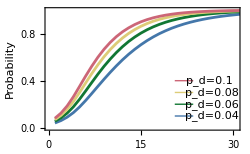

```mathematica
Show[ListLinePlot[{pend4,pend6,pend8,pend10},PlotRange->{{0,30.5},All},Frame->True,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Days after initial detection","Estimated probability outbreak has ended"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{20.5,0.4},{23.5,0.4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{20.5,0.3},{23.5,0.3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{20.5,0.2},{23.5,0.2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{20.5,0.1},{23.5,0.1}}]}],Graphics[Text["p_d=0.1",{26.2,0.4}]],Graphics[Text["p_d=0.08",{26.5,0.3}]],Graphics[Text["p_d=0.06",{26.5,0.2}]],Graphics[Text["p_d=0.04",{26.5,0.1}]]]
```

```mathematica
Population size conditional on not dying out at day 14
```

91

71

63

57

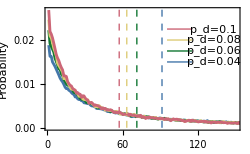

{0,0.018834,0.0351066,0.0513732,0.0663561,0.0808417,0.094794,0.108113,0.120791,0.132821,0.144148,0.154985,0.165432,0.175313,0.184565,0.193481,0.202407,0.210941,0.219337,0.227349,0.235079,0.242679,0.2497,0.256791,0.263381,0.269803,0.276279,0.282423,0.288616,0.294311,0.299961,0.305542,0.311036,0.31659,0.321803,0.326793,0.331759,0.336632,0.341351,0.345745,0.350262,0.354628,0.35895,0.363259,0.367451,0.371522,0.375611,0.379417,0.383099,0.386821,0.390392,0.394219,0.39782,0.401295,0.404646,0.408057,0.411456,0.414641,0.41792,0.421075,0.42423,0.427231,0.430215,0.433086,0.436064,0.438794,0.441612,0.444134,0.44671,0.449468,0.452201,0.45485,0.457426,0.460108,0.462715,0.465119,0.467768,0.470149,0.472653,0.474994,0.477327,0.479569,0.481877,0.484195,0.486479,0.488633,0.490848,0.492958,0.495073,0.497306,0.499512,0.501564,0.503679,0.505674,0.507717,0.509598,0.511529,0.513289,0.515248,0.517125,0.518964,0.520808,0.522444,0.524207,0.526,0.527778,0.52958,0.531271,0.532985,0.53476,0.536451,0.538111,0.539759,0.541438,0.543035,0.544463,0.546202,0.547697,0.549189,0.550674,0.552253,0.553663,0.555134,0.556587,0.558084,0.559597,0.560986,0.562625,0.564063,0.565416,0.566796,0.568221,0.569418,0.57065,0.572,0.573296,0.57461,0.575903,0.577256,0.578434,0.579718,0.580953,0.582324,0.583506,0.58469,0.585925,0.587191,0.588378,0.589581,0.590816,0.591937,0.593049,0.594107,0.595249,0.596289,0.597389,0.598573,0.599691,0.600779,0.601842,0.6029,0.60403,0.605079,0.606176,0.607312,0.608297,0.609231,0.610265,0.611323,0.612347,0.613281,0.614273,0.615267,0.61637,0.617326,0.618311,0.619227,0.620182,0.621053,0.621984,0.623,0.623931,0.624919,0.625832,0.626721,0.627638,0.628499,0.629397,0.630341,0.631151,0.632052,0.633026,0.633896,0.63477,0.635578,0.636518,0.637458,0.638221,0.639107,0.639963,0.640782,0.641451,0.642286,0.64303,0.643778,0.644624,0.645332,0.646164,0.64689,0.647716,0.648521,0.649371,0.650172,0.651034,0.651751,0.652474,0.653216,0.653975,0.654692,0.655379,0.656127,0.656805,0.657603,0.658263,0.658941,0.659692,0.660339,0.661036,0.661768,0.662479,0.663187,0.663883,0.664628,0.665348,0.665972,0.66658,0.667285,0.66793,0.66859,0.669166,0.669759,0.670456,0.671146,0.671751,0.67236,0.672975,0.673626,0.674307,0.674982,0.675645,0.676232,0.676901,0.677588,0.678209,0.678839,0.67952,0.680129,0.680701,0.681394,0.681994,0.682597,0.683233,0.68382,0.68442,0.684983,0.685568,0.686246,0.686819,0.687442,0.687985,0.688548,0.68907,0.689724,0.690347,0.69086,0.691405,0.69195,0.692544,0.693071,0.693635,0.694138,0.694638,0.695208,0.695817,0.696305,0.696844,0.697396,0.697872,0.698393,0.698927,0.699406,0.699927,0.700473,0.701018,0.701521,0.702088,0.702603,0.703127,0.703703,0.704212,0.704755,0.705285,0.705876,0.706361,0.70684,0.707292,0.707759,0.708241,0.708772,0.709269,0.709808,0.71023,0.710733,0.711212,0.711655,0.712098,0.712508,0.713002,0.71343,0.713867,0.714322,0.714829,0.715253,0.715699,0.716179,0.716667,0.71717,0.717649,0.718152,0.718616,0.719068,0.719469,0.719888,0.720337,0.72075,0.721169,0.721651,0.722073,0.722546,0.722959,0.723396,0.723845,0.724288,0.72474,0.725231,0.725683,0.726138,0.726593,0.727018,0.727404,0.727771,0.728178,0.728597,0.72895,0.72938,0.729805,0.730164,0.73058,0.730905,0.731321,0.731806,0.732177,0.732569,0.732985,0.73334,0.733693,0.734054,0.734434,0.734847,0.735266,0.735667,0.736022,0.736363,0.736715,0.737086,0.737429,0.737767,0.738129,0.738454,0.738834,0.739237,0.739575,0.7399,0.740271,0.740648,0.741037,0.741365,0.741721,0.742019,0.742459,0.742842,0.743188,0.74355,0.743893,0.744234,0.744604,0.744948,0.745291,0.745584,0.745894,0.746241,0.746651,0.746979,0.747329,0.74769,0.748049,0.748356,0.748706,0.749016,0.749396,0.74973,0.750083,0.750448,0.750773,0.751032,0.751346,0.751662,0.751966,0.752259,0.752512,0.752813,0.753123,0.753494,0.753798,0.754109,0.754425,0.754699,0.754992,0.755326,0.755667,0.756046,0.756366,0.756676,0.756954,0.757252,0.757517,0.757836,0.758129,0.758442,0.75871,0.758976,0.759262,0.759518,0.759804,0.76013,0.760404,0.760726,0.761025,0.761332,0.761645,0.76189,0.762212,0.762477,0.762806,0.763068,0.763336,0.763616,0.763887,0.764113,0.7644,0.764674,0.764993,0.765286,0.765494,0.765774,0.766054,0.766352,0.766612,0.766877,0.767154,0.767434,0.767706,0.768001,0.768254,0.768504,0.768739,0.769007,0.769254,0.769517,0.76977,0.770053,0.770312,0.770586,0.770894,0.771174,0.771415,0.771638,0.771918,0.772153,0.772413,0.772666,0.772895,0.773178,0.773413,0.773654,0.773898,0.774227,0.774468,0.774691,0.774944,0.77517,0.775426,0.775679,0.775923,0.7762,0.776451,0.776743,0.776984,0.777246,0.777487,0.777698,0.777909,0.778117,0.778349,0.77859,0.778867,0.779066,0.779244,0.779485,0.779738,0.779991,0.780235,0.780464,0.780712,0.780959,0.781164,0.781378,0.781625,0.781902,0.782134,0.782384,0.782577,0.782839,0.783056,0.783327,0.783559,0.78377,0.783966,0.784192,0.784439,0.784617,0.78484,0.785078,0.785319,0.785566,0.785786,0.786036,0.786265,0.786491,0.786741,0.786964,0.787196,0.787432,0.787652,0.787878,0.788088,0.788278,0.788489,0.788703,0.788962,0.789155,0.789363,0.789583,0.789785,0.789975,0.790228,0.790418,0.790662,0.790876,0.791108,0.791361,0.791581,0.791801,0.792027,0.792262,0.792479,0.79269,0.792898,0.793139,0.793356,0.793537,0.793778,0.793965,0.794215,0.794414,0.794643,0.794827,0.795001,0.79526,0.795471,0.795682,0.795866,0.796056,0.79624,0.796424,0.796595,0.7968,0.797035,0.797204,0.797427,0.797644,0.797849,0.798048,0.798232,0.798425,0.79862,0.798828,0.799045,0.799259,0.799422,0.799657,0.799844,0.800007,0.800209,0.800398,0.800594,0.800793,0.80101,0.801227,0.801423,0.801592,0.801739,0.801929,0.802143,0.802333,0.802508,0.802695,0.802836,0.803038,0.803255,0.803424,0.803614,0.803767,0.803963,0.804144,0.804361,0.804515,0.804747,0.804913,0.805069,0.805292,0.805446,0.805612,0.805801,0.805982,0.806193,0.806347,0.806516,0.80669,0.806847,0.806983,0.807145,0.807323,0.80751,0.807649,0.807839,0.808059,0.808227,0.80839,0.808553,0.808676,0.808857,0.80905,0.809216,0.809397,0.809553,0.809707,0.809867,0.810032,0.810201,0.810358,0.810521,0.810677,0.810834,0.811024,0.811162,0.811331,0.811458,0.81166,0.811859,0.812015,0.812163,0.812311,0.812467,0.81263,0.81279,0.812949,0.813088,0.813212,0.813398,0.813543,0.813739,0.813929,0.81411,0.814236,0.814402,0.814586,0.814733,0.814893,0.815062,0.815255,0.815414,0.815598,0.815749,0.815851,0.816047,0.816162,0.816309,0.816487,0.816647,0.816786,0.816909,0.817093,0.817253,0.817403,0.81756,0.817714,0.817882,0.818015,0.818175,0.818322,0.818491,0.818633,0.818768,0.818934,0.8191,0.819247,0.819431,0.819606,0.819772,0.819919,0.820079,0.820254,0.820429,0.820576,0.820712,0.820872,0.821031,0.821149,0.821273,0.821456,0.821574,0.821758,0.821914,0.822059,0.822204,0.82236,0.822502,0.822695,0.822824,0.822987,0.823174,0.823286,0.823391,0.823551,0.823692,0.823783,0.823933,0.824057,0.824214,0.824349,0.824467,0.824602,0.824777,0.824931,0.825066,0.825184,0.82535,0.825464,0.825612,0.825763,0.825892,0.826046,0.82619,0.826353,0.826522,0.826679,0.826829,0.826971,0.827125,0.827308,0.827435,0.827556,0.827673,0.827803,0.827956,0.828134,0.828291,0.82842,0.828574,0.82871,0.828854,0.82896,0.829092,0.829225,0.829321,0.829442,0.829581,0.829716,0.829855,0.829963,0.830087,0.830195,0.830364,0.830467,0.830605,0.830723,0.830855,0.830973,0.831081,0.831196,0.831356,0.831494,0.831612,0.831729,0.831844,0.831946,0.832085,0.832223,0.832368,0.83248,0.832621,0.832724,0.832889,0.833028,0.833164,0.833272,0.833405,0.833525,0.83367,0.833784,0.833923,0.834004,0.83411,0.834203,0.834345,0.834429,0.834592,0.834709,0.834791,0.834923,0.835074,0.835189,0.835324,0.835451,0.835562,0.835662,0.835764,0.835861,0.836002,0.836114,0.836213,0.83631,0.836406,0.836524,0.836659,0.836774,0.836888,0.836991,0.83709,0.837187,0.837325,0.837464,0.837572,0.837684,0.837804,0.837919,0.838,0.838109,0.838214,0.838317,0.838419,0.838543,0.83863,0.838732,0.838865,0.83894,0.839046,0.839157,0.839269,0.839413,0.839522,0.839642,0.839772,0.839878,0.839992,0.840079,0.840191,0.840314,0.840417,0.840498,0.840607,0.840718,0.840833,0.84095,0.841056,0.841158,0.841246,0.841363,0.841478,0.841571,0.841674,0.841809,0.841927,0.842017,0.842129,0.84227,0.842379,0.842493,0.842608,0.842716,0.842882,0.84296,0.843075,0.843177,0.843295,0.84337,0.843473,0.843578,0.84369,0.843825,0.843961,0.844048,0.844178,0.844262,0.844371,0.844497,0.844582,0.844711,0.84485,0.84494,0.845061,0.845199,0.845293,0.845407,0.845522,0.84563,0.845748,0.845853,0.845947,0.846043,0.846139,0.846254,0.846356,0.84645,0.846552,0.846661,0.846754,0.846863,0.846974,0.847107,0.847203,0.847351,0.847477,0.847583,0.847703,0.8478,0.847899,0.847981,0.848053,0.848192,0.848324,0.848442,0.848544,0.848638,0.848746,0.848815,0.848897,0.848963,0.849063,0.849186,0.849252,0.849385,0.849484,0.849584,0.849692,0.849786,0.849867,0.85,0.850114,0.850208,0.850289,0.850434,0.850512,0.850617,0.850717,0.85081,0.850904,0.851003,0.851079,0.851163,0.851265,0.851359,0.851458,0.851555,0.85166,0.851754,0.851862,0.851952,0.852067,0.85216,0.852239,0.852344,0.852444,0.852528,0.852639,0.852736,0.852832,0.852938,0.853022,0.853146,0.853242,0.853339,0.853417,0.853486,0.853568,0.853646,0.853745,0.853815,0.853884,0.85399,0.854092,0.854194,0.854261,0.854324,0.854429,0.85452,0.854646,0.854737,0.8548,0.854878,0.854951,0.85505,0.855141,0.855228,0.855321,0.855409,0.855493,0.85559,0.85568,0.855767,0.855852,0.855936,0.856033,0.856135,0.856241,0.85634,0.856452,0.856506,0.856593,0.85669,0.856801,0.856922,0.856985,0.857066,0.857154,0.857211,0.857298,0.857362,0.857455,0.857527,0.857636,0.857726,0.85782,0.857895,0.858009,0.858097,0.858178,0.858266,0.858344,0.858446,0.858516,0.8586,0.858675,0.858751,0.858841,0.858923,0.859022,0.859079,0.859152,0.859212,0.859263,0.859341,0.859426,0.859522,0.859604,0.859667,0.859772,0.859869,0.85995,0.860071,0.860182,0.860264,0.860351,0.860435,0.860514,0.860592,0.86067,0.860746,0.860833,0.860917,0.860975,0.861068,0.861149,0.861246,0.861303,0.861375,0.861466,0.861526,0.861632,0.861689,0.861809,0.861894,0.861939,0.86205,0.862132,0.862204,0.862322,0.8624,0.862445,0.862512,0.862578,0.862638,0.862698,0.862774,0.86287,0.862924,0.863003,0.863093,0.863178,0.863274,0.863376,0.863476,0.863542,0.863614,0.863714,0.86381,0.863889,0.863955,0.864079,0.864151,0.864226,0.864271,0.864338,0.864416,0.864491,0.864582,0.864666,0.864745,0.864847,0.864934,0.865013,0.865106,0.865191,0.865278,0.865332,0.865413,0.865468,0.865534,0.865606,0.865688,0.865772,0.865847,0.865929,0.865998,0.866064,0.866167,0.866248,0.866308,0.866384,0.866471,0.866544,0.866595,0.866658,0.866712,0.866776,0.866854,0.866944,0.867002,0.86708,0.867137,0.867191,0.867246,0.867306,0.867393,0.867478,0.867553,0.867628,0.867701,0.867773,0.867845,0.867912,0.867999,0.86805,0.868117,0.868201,0.868288,0.868346,0.868418,0.868484,0.86856,0.868629,0.868713,0.868789,0.868861,0.868918,0.868999,0.869087,0.869132,0.869201,0.869277,0.869316,0.869403,0.869473,0.869569,0.869638,0.869699,0.869756,0.86984,0.869894,0.869958,0.870021,0.870096,0.87019,0.870268,0.870353,0.870434,0.87053,0.870576,0.870642,0.870726,0.870768,0.870838,0.870892,0.870931,0.870997,0.871058,0.871139,0.871196,0.87126,0.871353,0.871428,0.871528,0.871612,0.871645,0.871718,0.871763,0.871841,0.871907,0.871998,0.872046,0.872118,0.872203,0.872266,0.872332,0.872393,0.872471,0.872519,0.872592,0.872631,0.872688,0.872733,0.872812,0.872908,0.872968,0.873028,0.873104,0.87317,0.873248,0.873321,0.873378,0.873444,0.873517,0.873592,0.873652,0.873728,0.873827,0.873908,0.873948,0.873999,0.874065,0.874122,0.874189,0.874249,0.874303,0.874382,0.874424,0.874487,0.874547,0.874653,0.874716,0.874785,0.874846,0.874897,0.874951,0.875008,0.875069,0.875138,0.875228,0.875304,0.87537,0.875439,0.875493,0.875584,0.875644,0.875704,0.875765,0.875852,0.875909,0.87597,0.876042,0.876099,0.87615,0.876226,0.876274,0.876343,0.876391,0.876461,0.876518,0.876581,0.876614,0.876669,0.876741,0.876795,0.876837,0.87688,0.876928,0.876979,0.877036,0.8771,0.877145,0.877196,0.877262,0.877323,0.877389,0.877446,0.877506,0.877561,0.877606,0.877669,0.877705,0.877769,0.877841,0.877931,0.878001,0.878058,0.878106,0.878175,0.87826,0.878332,0.878386,0.878456,0.878516,0.878573,0.87863,0.878676,0.878757,0.878841,0.878923,0.878971,0.879019,0.879061,0.879119,0.879203,0.879242,0.879278,0.879339,0.879408,0.879474,0.879559,0.879601,0.879679,0.879724,0.879797,0.879857,0.87992,0.879965,0.880023,0.880068,0.880131,0.880149,0.880191,0.880237,0.880285,0.880342,0.880408,0.880457,0.880508,0.880556,0.88061,0.880662,0.880719,0.880746,0.880791,0.880866,0.880906,0.880978,0.881044,0.881105,0.881144,0.881198,0.88124,0.8813,0.881349,0.881427,0.881469,0.881514,0.88156,0.881614,0.881659,0.881713,0.881749,0.88178,0.88184,0.881903,0.88196,0.882012,0.882051,0.88209,0.882144,0.882189,0.882235,0.882286,0.882352,0.882427,0.882476,0.882539,0.882587,0.882632,0.88269,0.882741,0.882783,0.882825,0.882894,0.882955,0.883006,0.883045,0.883142,0.883184,0.883235,0.883298,0.883353,0.883419,0.883491,0.883551,0.883591,0.883648,0.883705,0.883768,0.883817,0.883868,0.883919,0.883952,0.884028,0.88407,0.884106,0.88416,0.884208,0.884245,0.884272,0.884332,0.884395,0.884446,0.884504,0.884567,0.884636,0.884694,0.88476,0.884814,0.884871,0.884907,0.884941,0.884992,0.885043,0.885091,0.885158,0.885182,0.885221,0.88529,0.885344,0.885423,0.885474,0.885534,0.885576,0.885613,0.885679,0.885724,0.885757,0.885812,0.885854,0.885911,0.885962,0.886035,0.886068,0.886116,0.886167,0.886209,0.886258,0.886333,0.886393,0.886462,0.886511,0.886562,0.886604,0.886661,0.886734,0.886785,0.886827,0.886896,0.886945,0.886993,0.88705,0.887095,0.887137,0.88721,0.887267,0.887312,0.887363,0.887409,0.887454,0.887511,0.887562,0.887629,0.887671,0.887713,0.887743,0.8878,0.887828,0.887885,0.887909,0.887966,0.887996,0.888051,0.888111,0.888141,0.888207,0.88824,0.888277,0.88831,0.888376,0.888433,0.888472,0.888506,0.888545,0.888572,0.888629,0.888692,0.888756,0.888789,0.888855,0.888894,0.888942,0.888994,0.889048,0.889087,0.889135,0.889181,0.88922,0.889256,0.88931,0.889352,0.889391,0.889419,0.88947,0.889494,0.88956,0.889633,0.889708,0.889762,0.889801,0.88985,0.88988,0.889919,0.889955,0.889994,0.890042,0.890085,0.890127,0.890169,0.890223,0.89025,0.890302,0.890365,0.890395,0.890446,0.89047,0.890531,0.890582,0.890618,0.890645,0.890696,0.890748,0.890799,0.890853,0.890889,0.890943,0.890977,0.891022,0.891076,0.891127,0.891175,0.891215,0.891269,0.891308,0.891368,0.89142,0.89148,0.891519,0.891588,0.891633,0.891691,0.891742,0.891784,0.891817,0.891878,0.89192,0.891965,0.892013,0.892052,0.892104,0.892128,0.892206,0.892248,0.892278,0.892333,0.892372,0.892405,0.892459,0.892513,0.892553,0.892598,0.89264,0.892691,0.892754,0.892803,0.892872,0.892914,0.892953,0.892996,0.89305,0.89308,0.893143,0.893182,0.893213,0.893246,0.893276,0.893333,0.893372,0.893414,0.893442,0.893472,0.893514,0.89355,0.89361,0.893659,0.893725,0.893764,0.893806,0.893854,0.893882,0.893918,0.893966,0.893993,0.894026,0.894083,0.894111,0.894174,0.894213,0.894252,0.894303,0.894331,0.894367,0.894412,0.894439,0.894493,0.894538,0.894581,0.894608,0.894632,0.894671,0.894746,0.894801,0.894837,0.8949,0.894936,0.894993,0.89503,0.895081,0.895138,0.895183,0.895232,0.895274,0.895304,0.895343,0.895376,0.895424,0.895494,0.89553,0.895602,0.895629,0.895675,0.895699,0.895738,0.895783,0.895807,0.89584,0.895879,0.895916,0.895961,0.896015,0.896048,0.896099,0.896163,0.896187,0.896241,0.896286,0.896316,0.896374,0.89641,0.896458,0.8965,0.896567,0.896615,0.896636,0.896678,0.896738,0.896765,0.896805,0.896844,0.896868,0.896931,0.896988,0.897019,0.897079,0.897109,0.897145,0.897184,0.897223,0.897278,0.897314,0.897353,0.897407,0.897431,0.897465,0.897525,0.897576,0.89763,0.897669,0.897709,0.897757,0.897808,0.897862,0.897886,0.897929,0.897968,0.898016,0.898088,0.898118,0.898149,0.898182,0.898233,0.898281,0.898323,0.898347,0.898402,0.89845,0.898492,0.898516,0.898537,0.898589,0.898619,0.898673,0.898703,0.898739,0.89879,0.898805,0.898857,0.898884,0.898926,0.898962,0.899007,0.899031,0.899077,0.899137,0.899176,0.899224,0.899279,0.8993,0.899333,0.899366,0.899402,0.899444,0.899487,0.899538,0.899574,0.899607,0.899628,0.899658,0.899694,0.899743,0.899785,0.899827,0.899842,0.899887,0.89993,0.899969,0.900014,0.900056,0.900098,0.900122,0.900171,0.900198,0.900225,0.900246,0.900285,0.900315,0.900342,0.900382,0.900406,0.900451,0.900478,0.900511,0.900541,0.900592,0.900614,0.900653,0.900698,0.900743,0.900788,0.9008,0.900843,0.900888,0.900924,0.90096,0.901014,0.901051,0.901096,0.901147,0.901189,0.901255,0.90128,0.901325,0.901361,0.901409,0.901457,0.901475,0.901521,0.901578,0.901617,0.901644,0.901677,0.901704,0.901744,0.90178,0.90181,0.901846,0.90187,0.901891,0.901936,0.901964,0.902009,0.902036,0.90206,0.902093,0.902126,0.902153,0.902168,0.902196,0.902238,0.902277,0.902319,0.902358,0.902391,0.90244,0.902488,0.902536,0.90259,0.902642,0.902684,0.902717,0.902768,0.902798,0.902837,0.90288,0.902922,0.902955,0.902988,0.903033,0.903073,0.903118,0.903139,0.90319,0.903214,0.90325,0.903265,0.903311,0.903353,0.903407,0.903446,0.903473,0.9035,0.903549,0.903588,0.903627,0.903666,0.903693,0.903742,0.903787,0.903832,0.903856,0.903874,0.903904,0.903934,0.903961,0.90401,0.904046,0.904064,0.9041,0.904127,0.904166,0.904197,0.904248,0.90429,0.904332,0.904365,0.904423,0.904447,0.904486,0.904507,0.904534,0.904576,0.904603,0.904649,0.90467,0.904706,0.904754,0.904784,0.904814,0.904841,0.904866,0.904893,0.904908,0.904932,0.904992,0.905037,0.905076,0.905107,0.905152,0.905188,0.905224,0.905257,0.905275,0.905305,0.905336,0.905393,0.905417,0.905447,0.905483,0.905538,0.905568,0.90561,0.905655,0.905682,0.905724,0.905779,0.905806,0.905854,0.905896,0.905938,0.905974,0.90599,0.906032,0.906065,0.906098,0.906122,0.906161,0.906182,0.906216,0.906258,0.906291,0.906315,0.906339,0.906372,0.906417,0.906463,0.906484,0.906526,0.906562,0.906595,0.906646,0.906692,0.90674,0.906791,0.906824,0.906869,0.906888,0.906918,0.906951,0.906981,0.907026,0.907053,0.907077,0.907086,0.907126,0.907165,0.907198,0.90727,0.907312,0.907361,0.907409,0.907448,0.90746,0.907493,0.907532,0.907563,0.907584,0.907611,0.907653,0.90768,0.907701,0.907731,0.907761,0.907807,0.907834,0.907873,0.907906,0.907945,0.907972,0.908015,0.908033,0.908066,0.90809,0.908129,0.908162,0.908189,0.908223,0.908265,0.908301,0.908328,0.90837,0.908403,0.908439,0.908479,0.908506,0.908551,0.90859,0.908635,0.908665,0.908702,0.908744,0.908768,0.908807,0.908837,0.908867,0.908885,0.908931,0.908961,0.909009,0.909027,0.909075,0.909096,0.909124,0.909148,0.909175,0.909214,0.909253,0.909286,0.909307,0.909325,0.909347,0.909386,0.90944,0.909464,0.909506,0.90953,0.90956,0.909594,0.909618,0.909642,0.90966,0.90969,0.909708,0.90972,0.909759,0.909783,0.909802,0.909847,0.90991,0.909943,0.909973,0.910012,0.910031,0.910067,0.9101,0.910139,0.910163,0.910202,0.910217,0.910242,0.910257,0.910296,0.910341,0.91038,0.910404,0.910434,0.910455,0.910486,0.910513,0.91054,0.91057,0.910618,0.910642,0.910675,0.910703,0.910739,0.910769,0.910778,0.910808,0.910847,0.910871,0.910914,0.910935,0.910971,0.911004,0.911034,0.911049,0.911088,0.911106,0.91114,0.911164,0.911191,0.911212,0.911239,0.911269,0.911293,0.91132,0.911344,0.911384,0.911405,0.911432,0.911456,0.911507,0.911531,0.911589,0.91161,0.911628,0.911655,0.911688,0.911697,0.911721,0.911745,0.911775,0.911809,0.911851,0.911881,0.911896,0.911935,0.91195,0.911989,0.912013,0.912047,0.912059,0.912098,0.912122,0.912143,0.912176,0.9122,0.912224,0.912264,0.912288,0.912327,0.912351,0.91239,0.912423,0.912447,0.912465,0.912477,0.912505,0.912535,0.912589,0.912619,0.912643,0.912676,0.91271,0.91274,0.912779,0.912797,0.912824,0.912857,0.912875,0.912902,0.912923,0.912957,0.912972,0.912999,0.913047,0.913083,0.913101,0.913131,0.913162,0.913201,0.913222,0.913264,0.913291,0.913321,0.91336,0.913382,0.913415,0.913439,0.913466,0.913484,0.91352,0.913553,0.913577,0.913614,0.913656,0.913674,0.913698,0.913716,0.913752,0.913791,0.913818,0.913849,0.913879,0.913918,0.913951,0.913978,0.914011,0.914029,0.914057,0.914081,0.914114,0.914141,0.914183,0.91421,0.914222,0.914252,0.914289,0.914316,0.914343,0.914358,0.914385,0.914409,0.914442,0.914475,0.914518,0.914545,0.914566,0.914587,0.914623,0.91465,0.914665,0.914683,0.914723,0.914762,0.914783,0.914819,0.914852,0.914882,0.914918,0.914939,0.914958,0.914988,0.915,0.91503,0.91506,0.915084,0.915129,0.91515,0.915178,0.915196,0.915211,0.915229,0.915265,0.915304,0.915334,0.915358,0.915382,0.915407,0.915437,0.915467,0.915497,0.915518,0.915536,0.915569,0.91559,0.915602,0.915633,0.915663,0.915693,0.915714,0.91575,0.915765,0.915801,0.915825,0.915847,0.915862,0.915895,0.91591,0.915943,0.915976,0.915991,0.916012,0.916036,0.916051,0.916082,0.916097,0.916115,0.916154,0.916172,0.916199,0.916226,0.91625,0.916271,0.91629,0.916308,0.916335,0.91635,0.916377,0.916401,0.916422,0.916443,0.916467,0.916482,0.916522,0.916546,0.916567,0.916591,0.916612,0.916633,0.916645,0.91666,0.916678,0.916699,0.91672,0.916754,0.916775,0.916799,0.916826,0.916862,0.916892,0.91694,0.916971,0.917001,0.917031,0.917073,0.917091,0.917121,0.917145,0.91716,0.917197,0.917218,0.917248,0.917287,0.917305,0.917332,0.917371,0.917383,0.917423,0.917444,0.917471,0.917498,0.917522,0.917564,0.917585,0.917609,0.917655,0.917697,0.91773,0.917748,0.917766,0.917796,0.91782,0.917829,0.917866,0.917896,0.917905,0.917932,0.917965,0.917977,0.918016,0.918031,0.918058,0.918086,0.91811,0.918149,0.918179,0.918206,0.918242,0.918266,0.918275,0.918302,0.918321,0.918345,0.918363,0.918396,0.91842,0.918429,0.918453,0.918477,0.918489,0.918498,0.918528,0.918553,0.918583,0.918604,0.918646,0.918673,0.918703,0.918724,0.918755,0.918776,0.918809,0.918827,0.918842,0.918869,0.918881,0.918887,0.918914,0.918932,0.91895,0.918993,0.919023,0.919047,0.919065,0.919122,0.919155,0.919179,0.919204,0.919219,0.919258,0.91927,0.919297,0.919315,0.919336,0.919357,0.919372,0.91939,0.919433,0.919451,0.919466,0.919499,0.919532,0.91955,0.919577,0.919595,0.919616,0.919656,0.919671,0.919692,0.919725,0.919764,0.919782,0.919803,0.919827,0.919848,0.91986,0.919891,0.919927,0.919939,0.919954,0.919972,0.919999,0.920032,0.92005,0.920074,0.920099,0.920123,0.920132,0.920159,0.92018,0.920201,0.920234,0.920249,0.920276,0.920297,0.920315,0.920343,0.920364,0.920391,0.920415,0.920454,0.920475,0.920496,0.92052,0.920548,0.920584,0.920629,0.92065,0.920674,0.920707,0.920725,0.920743,0.920761,0.920777,0.920789,0.920813,0.920831,0.920852,0.92087,0.920888,0.920909,0.920936,0.92096,0.920987,0.921012,0.921027,0.921054,0.921078,0.921096,0.921117,0.921144,0.921165,0.921198,0.921213,0.921226,0.921253,0.92128,0.92131,0.92134,0.921349,0.921373,0.921397,0.921421,0.921446,0.921479,0.921506,0.921551,0.921578,0.921596,0.921629,0.921656,0.921675,0.921699,0.921714,0.921723,0.921738,0.921765,0.921792,0.921831,0.921855,0.921876,0.921892,0.921916,0.921934,0.921958,0.921973,0.921994,0.922021,0.922045,0.922081,0.922105,0.922124,0.922154,0.922166,0.922178,0.922193,0.922205,0.922244,0.922265,0.922289,0.922313,0.922344,0.922374,0.922401,0.92241,0.922434,0.922461,0.922482,0.9225,0.922515,0.922545,0.922582,0.922582,0.922588,0.922612,0.922651,0.922681,0.922693,0.922711,0.922753,0.922765,0.922777,0.922805,0.922823,0.92285,0.922871,0.922886,0.922916,0.922928,0.922946,0.922982,0.923006,0.923031,0.923052,0.923082,0.923097,0.923127,0.923154,0.923181,0.923202,0.923239,0.923248,0.923281,0.923308,0.923326,0.92335,0.923383,0.923404,0.923416,0.923437,0.923458,0.92348,0.923498,0.923513,0.923546,0.923564,0.923591,0.923606,0.923627,0.923639,0.923666,0.923681,0.9237,0.923721,0.923739,0.92376,0.923775,0.923793,0.923817,0.923835,0.923874,0.923892,0.923911,0.923926,0.92395,0.923977,0.923998,0.924025,0.924031,0.924067,0.924097,0.924124,0.924167,0.924203,0.924227,0.924248,0.924272,0.924284,0.924311,0.924341,0.924372,0.924393,0.924414,0.924444,0.924459,0.924474,0.924495,0.924522,0.924561,0.924586,0.924601,0.924628,0.924664,0.924694,0.924718,0.924742,0.924757,0.924772,0.924784,0.924815,0.924827,0.924836,0.924854,0.924887,0.924923,0.924938,0.924977,0.925001,0.925013,0.925041,0.925071,0.925098,0.92511,0.925134,0.925146,0.925155,0.925167,0.925182,0.925203,0.925224,0.925245,0.925267,0.925279,0.925306,0.925333,0.925354,0.925396,0.925411,0.925438,0.925465,0.925496,0.925526,0.925544,0.925556,0.925583,0.925598,0.92561,0.925637,0.925658,0.925679,0.925697,0.925731,0.925746,0.92577,0.925806,0.925827,0.925848,0.925872,0.925884,0.925896,0.92592,0.925936,0.925966,0.925978,0.925984,0.926002,0.926029,0.926044,0.926053,0.92608,0.926104,0.92611,0.926131,0.92615,0.926159,0.926183,0.92621,0.926225,0.926246,0.926258,0.926288,0.926315,0.926333,0.926348,0.92636,0.926391,0.926412,0.92643,0.926457,0.926478,0.926502,0.926523,0.926553,0.926571,0.926595,0.92662,0.926644,0.926668,0.92668,0.926707,0.926725,0.926749,0.926767,0.926785,0.926809,0.926831,0.926846,0.926879,0.926897,0.926915,0.926933,0.926948,0.926972,0.927002,0.927029,0.927041,0.92706,0.927075,0.927108,0.927126,0.927141,0.927174,0.927192,0.92721,0.927228,0.927249,0.927274,0.927295,0.927325,0.927337,0.927352,0.927373,0.927394,0.927424,0.927436,0.927451,0.92746,0.927475,0.927484,0.9275,0.927512,0.927533,0.927542,0.927563,0.927578,0.927596,0.92762,0.927644,0.927665,0.927677,0.927689,0.927701,0.92771,0.927732,0.92775,0.927756,0.927795,0.927816,0.927843,0.927858,0.927876,0.9279,0.927918,0.927939,0.927949,0.927973,0.927991,0.928003,0.928033,0.928057,0.928069,0.92809,0.928114,0.92815,0.928169,0.928181,0.928196,0.928217,0.928232,0.92825,0.928268,0.928298,0.928325,0.928346,0.928364,0.928376,0.928407,0.928419,0.928428,0.928443,0.928458,0.928476,0.928497,0.928512,0.928521,0.928536,0.92856,0.92859,0.928602,0.928618,0.928636,0.928666,0.928684,0.928696,0.928708,0.928738,0.928765,0.928777,0.928792,0.928804,0.928822,0.928834,0.928862,0.928874,0.928901,0.928922,0.928949,0.928961,0.928976,0.929006,0.929015,0.92903,0.929039,0.929057,0.929076,0.929097,0.929115,0.929142,0.929166,0.929196,0.929208,0.92922,0.929238,0.929256,0.929274,0.929302,0.929326,0.929338,0.929353,0.929383,0.929398,0.929422,0.929434,0.929449,0.929479,0.929503,0.929522,0.929537,0.929552,0.929567,0.929576,0.929594,0.929615,0.929639,0.929654,0.929663,0.929678,0.929684,0.929708,0.929729,0.929742,0.929763,0.929793,0.929796,0.92982,0.929844,0.929859,0.929871,0.929895,0.929907,0.929922,0.929949,0.929965,0.929986,0.929992,0.930019,0.930028,0.930046,0.930061,0.93007,0.930085,0.930109,0.930118,0.93013,0.930142,0.930154,0.930175,0.930191,0.930209,0.930224,0.930242,0.930269,0.93029,0.930305,0.930332,0.930347,0.930365,0.930377,0.930389,0.930423,0.930432,0.930453,0.930468,0.930492,0.930507,0.93054,0.930555,0.930573,0.930603,0.930621,0.930646,0.93067,0.930685,0.930691,0.930709,0.930727,0.930751,0.930769,0.930778,0.930802,0.930826,0.930844,0.93086,0.930875,0.930893,0.930908,0.930917,0.930932,0.930953,0.930977,0.930998,0.93101,0.931022,0.931037,0.931052,0.93107,0.93108,0.931101,0.931128,0.931146,0.931161,0.931176,0.931191,0.931206,0.931227,0.931257,0.931272,0.93129,0.931306,0.931321,0.931327,0.931339,0.931354,0.931369,0.931378,0.931384,0.931402,0.931423,0.931447,0.931474,0.931492,0.93151,0.931525,0.931547,0.931568,0.931577,0.931592,0.931607,0.931628,0.931643,0.931667,0.931688,0.931709,0.931739,0.931755,0.931776,0.931803,0.931812,0.931827,0.931848,0.931869,0.931875,0.931887,0.931899,0.931926,0.931944,0.931965,0.931978,0.931999,0.932023,0.932032,0.932053,0.932092,0.932107,0.932131,0.932146,0.932167,0.932176,0.932197,0.932222,0.932231,0.93224,0.932261,0.932282,0.932291,0.932309,0.932324,0.932333,0.932345,0.932366,0.932393,0.932411,0.93242,0.932445,0.93246,0.932484,0.932499,0.932526,0.932547,0.932568,0.93258,0.932598,0.932613,0.932631,0.93265,0.932656,0.932686,0.932704,0.932722,0.932758,0.932779,0.9328,0.932815,0.932827,0.932839,0.932857,0.932866,0.932885,0.932906,0.932918,0.932936,0.932957,0.932978,0.933014,0.933038,0.933047,0.933065,0.933074,0.933099,0.933105,0.933117,0.933132,0.933132,0.933147,0.933159,0.933174,0.933192,0.933198,0.933213,0.93324,0.933255,0.933279,0.933303,0.933318,0.933331,0.933358,0.933382,0.933391,0.933418,0.933436,0.933451,0.933466,0.933493,0.933517,0.933526,0.933538,0.933569,0.933578,0.933608,0.93362,0.933647,0.933665,0.93368,0.933692,0.933701,0.933731,0.933758,0.933771,0.933792,0.933801,0.933825,0.93384,0.933861,0.933891,0.933915,0.93393,0.933942,0.93396,0.933966,0.933981,0.933997,0.934,0.934021,0.934033,0.934048,0.934066,0.934072,0.934102,0.934117,0.934147,0.934165,0.934186,0.934201,0.934223,0.934238,0.934247,0.934274,0.934286,0.934295,0.934328,0.934337,0.934352,0.934367,0.934388,0.934412,0.934424,0.934439,0.934452,0.934473,0.934509,0.934521,0.934533,0.934551,0.934569,0.934575,0.93459,0.934605,0.934632,0.934647,0.934669,0.934699,0.93472,0.934747,0.93478,0.934801,0.934813,0.934831,0.934834,0.934846,0.934861,0.934888,0.934919,0.934943,0.934979,0.934988,0.935003,0.935015,0.935027,0.935051,0.935072,0.93509,0.935111,0.935142,0.935157,0.935181,0.935193,0.935208,0.935214,0.935238,0.935253,0.935271,0.935289,0.935298,0.935322,0.935347,0.935362,0.93538,0.935404,0.935422,0.935434,0.935446,0.935458,0.935467,0.935488,0.935503,0.935524,0.935548,0.935564,0.935585,0.935606,0.93563,0.935648,0.935669,0.935681,0.935684,0.935696,0.935714,0.935738,0.93575,0.935765,0.935787,0.935799,0.935823,0.935847,0.935868,0.935889,0.93591,0.935922,0.935949,0.935967,0.935985,0.936,0.936019,0.936043,0.936064,0.936079,0.9361,0.936118,0.936136,0.936154,0.936169,0.936178,0.936199,0.936205,0.936214,0.936239,0.936269,0.936287,0.936305,0.936317,0.936326,0.936341,0.936359,0.936371,0.936389,0.936395,0.936413,0.936428,0.93644,0.936462,0.936474,0.936492,0.936513,0.936531,0.936552,0.936573,0.9366,0.936612,0.93663,0.936651,0.93666,0.936685,0.936694,0.936703,0.936721,0.93673,0.936748,0.936769,0.93679,0.936808,0.936826,0.936853,0.936868,0.936886,0.936895,0.936917,0.936929,0.936944,0.936953,0.936965,0.936983,0.936992,0.936998,0.93701,0.937037,0.937052,0.937067,0.937079,0.937088,0.937088,0.937106,0.937121,0.937127,0.937146,0.93717,0.937194,0.937206,0.937215,0.93723,0.937248,0.937257,0.93729,0.937305,0.937317,0.937338,0.937353,0.93736,0.937369,0.937381,0.937387,0.937408,0.937435,0.937453,0.937477,0.937483,0.937495,0.937519,0.937519,0.93754,0.937558,0.937586,0.937604,0.937607,0.937631,0.937637,0.937646,0.937658,0.937679,0.937694,0.937715,0.937715,0.93773,0.937754,0.937772,0.93779,0.937812,0.937839,0.937851,0.937872,0.937893,0.937917,0.937941,0.937965,0.937986,0.937998,0.93801,0.938029,0.93805,0.938053,0.938071,0.93808,0.938101,0.938107,0.938125,0.938146,0.938158,0.938179,0.938188,0.938191,0.9382,0.938212,0.938224,0.938245,0.938252,0.93827,0.938273,0.938291,0.938306,0.938327,0.938348,0.938357,0.938381,0.938393,0.938411,0.93842,0.93842,0.938435,0.93845,0.938468,0.938487,0.938499,0.938529,0.93855,0.938574,0.938589,0.93861,0.938628,0.938637,0.938646,0.938658,0.938667,0.938685,0.938701,0.938713,0.938728,0.938746,0.938758,0.938782,0.938797,0.938815,0.938833,0.938851,0.938878,0.938884,0.938905,0.938917,0.93893,0.938948,0.938957,0.938987,0.938996,0.939002,0.93902,0.939041,0.939056,0.939068,0.939092,0.939104,0.939116,0.939134,0.93915,0.939165,0.939177,0.939189,0.939207,0.939231,0.939249,0.939258,0.939279,0.939297,0.939324,0.939345,0.939363,0.939379,0.9394,0.939424,0.939427,0.939427,0.93943,0.93946,0.939466,0.939478,0.939487,0.939514,0.93952,0.939532,0.939553,0.939571,0.939586,0.939602,0.939626,0.939641,0.93965,0.939674,0.939683,0.939692,0.93971,0.93974,0.939752,0.939761,0.93977,0.939791,0.939815,0.939831,0.939843,0.939855,0.939858,0.939861,0.939879,0.939885,0.939891,0.939915,0.93993,0.939936,0.939963,0.939969,0.939984,0.940002,0.940023,0.940045,0.94006,0.940087,0.940108,0.940114,0.940132,0.940156,0.94018,0.940186,0.940204,0.94021,0.940225,0.940231,0.940249,0.940255,0.940283,0.940307,0.940313,0.94034,0.940352,0.940361,0.940376,0.940394,0.940409,0.940427,0.940451,0.940466,0.940484,0.9405,0.940509,0.940521,0.940533,0.94056,0.940593,0.940611,0.940617,0.940632,0.940653,0.940665,0.940677,0.940695,0.940707,0.94072,0.940741,0.940765,0.940771,0.940789,0.940804,0.940822,0.940834,0.940852,0.940864,0.940879,0.940894,0.940915,0.940921,0.94093,0.940952,0.940958,0.940979,0.940982,0.941,0.941015,0.941042,0.941057,0.941063,0.941081,0.941093,0.941105,0.941117,0.941135,0.941147,0.941156,0.941169,0.941193,0.941214,0.941232,0.941241,0.941256,0.941265,0.941274,0.941292,0.941307,0.941319,0.941331,0.94134,0.941346,0.94137,0.941376,0.941389,0.941401,0.941416,0.941431,0.94144,0.941464,0.941467,0.941482,0.941503,0.941512,0.94153,0.941548,0.941551,0.94156,0.941587,0.941605,0.941633,0.941648,0.94166,0.941672,0.941687,0.941705,0.941723,0.941738,0.941753,0.941765,0.941789,0.941807,0.941828,0.941838,0.941847,0.941856,0.941886,0.941901,0.941922,0.941934,0.94194,0.941958,0.941982,0.942003,0.942021,0.942048,0.942057,0.942082,0.942109,0.942124,0.942136,0.942145,0.94216,0.942175,0.942187,0.94219,0.942205,0.942226,0.942247,0.942256,0.942296,0.942317,0.942341,0.942356,0.942368,0.94238,0.942395,0.942404,0.942425,0.942443,0.942458,0.942479,0.942497,0.94251,0.942528,0.942546,0.942546,0.942561,0.942585,0.9426,0.942618,0.942633,0.942642,0.942651,0.942672,0.942693,0.942699,0.942708,0.94272,0.942729,0.942733,0.942742,0.942754,0.942763,0.942772,0.942793,0.942805,0.94282,0.942835,0.942847,0.942853,0.942856,0.942874,0.942901,0.942922,0.942931,0.942943,0.942962,0.942983,0.943004,0.943013,0.943025,0.943034,0.943055,0.943085,0.943112,0.943127,0.943145,0.943151,0.943166,0.943182,0.943191,0.9432,0.943209,0.943224,0.943236,0.943269,0.943278,0.943281,0.943296,0.943323,0.943347,0.943356,0.943362,0.943386,0.943395,0.943414,0.943426,0.943438,0.943459,0.943477,0.943495,0.943498,0.943501,0.943519,0.943534,0.943561,0.943573,0.943588,0.9436,0.943612,0.94364,0.943655,0.943667,0.943676,0.943682,0.943691,0.943709,0.943727,0.943742,0.943763,0.943772,0.943781,0.94379,0.943817,0.943832,0.94386,0.943887,0.943902,0.94392,0.943938,0.943947,0.943962,0.943974,0.943995,0.944004,0.944007,0.944028,0.944037,0.944046,0.944055,0.944067,0.944073,0.944095,0.944107,0.944116,0.944143,0.94417,0.944185,0.9442,0.944215,0.944239,0.944251,0.944257,0.944263,0.944275,0.944281,0.944299,0.944309,0.944336,0.944354,0.944387,0.944399,0.944414,0.944426,0.944453,0.944471,0.944486,0.944495,0.944501,0.944522,0.944535,0.944556,0.94458,0.944592,0.94461,0.944622,0.944637,0.944646,0.944676,0.944685,0.944688,0.944694,0.9447,0.944721,0.944736,0.944742,0.94477,0.944794,0.9448,0.944809,0.944821,0.944836,0.94486,0.944872,0.944881,0.944905,0.944911,0.944938,0.944959,0.944965,0.944971,0.944981,0.945008,0.945029,0.945047,0.945065,0.945068,0.945074,0.94508,0.945101,0.94511,0.945119,0.945149,0.945164,0.945176,0.945185,0.945197,0.94521,0.945228,0.945243,0.945264,0.94527,0.945285,0.945297,0.945309,0.94533,0.945345,0.945354,0.945372,0.945381,0.94539,0.945414,0.94543,0.945445,0.945448,0.94546,0.945475,0.94549,0.945505,0.945535,0.94555,0.945568,0.945604,0.945619,0.945634,0.945653,0.945665,0.945671,0.945695,0.94571,0.945719,0.945728,0.94574,0.94574,0.945749,0.945776,0.945797,0.945818,0.945824,0.945842,0.945848,0.94586,0.945891,0.945903,0.945921,0.945936,0.945942,0.945948,0.945963,0.945978,0.945993,0.94602,0.946026,0.946044,0.94605,0.946062,0.946077,0.946092,0.946102,0.94612,0.946132,0.946153,0.946165,0.94618,0.946204,0.946216,0.946234,0.946255,0.94627,0.946282,0.946291,0.946319,0.94634,0.946358,0.946376,0.946385,0.946406,0.946433,0.946457,0.946472,0.946484,0.946508,0.946526,0.946545,0.946557,0.946569,0.946578,0.946587,0.946608,0.946638,0.946653,0.946668,0.946695,0.946704,0.946719,0.946731,0.946755,0.946777,0.946786,0.946798,0.946813,0.946825,0.946834,0.946846,0.946861,0.946873,0.946888,0.946909,0.946921,0.946933,0.946939,0.946951,0.946963,0.946981,0.946981,0.946997,0.947018,0.947039,0.947054,0.947075,0.947078,0.947081,0.947099,0.947105,0.947108,0.947117,0.947132,0.947141,0.947156,0.947177,0.947189,0.947204,0.94721,0.94722,0.947232,0.947241,0.947244,0.947256,0.947268,0.947283,0.947295,0.947334,0.947337,0.947355,0.947379,0.947391,0.947394,0.947403,0.947427,0.947452,0.94747,0.947476,0.947491,0.947503,0.947518,0.947536,0.947545,0.947554,0.947575,0.947584,0.947596,0.947608,0.947629,0.947644,0.947659,0.947675,0.947687,0.947699,0.947705,0.947717,0.947726,0.947741,0.947753,0.947771,0.947789,0.94781,0.947834,0.94784,0.947846,0.947849,0.947864,0.947876,0.947892,0.947901,0.947922,0.947928,0.94794,0.947949,0.947958,0.94797,0.947985,0.948003,0.948018,0.94803,0.948054,0.948069,0.948096,0.948124,0.94813,0.948145,0.948163,0.948178,0.948199,0.948208,0.948214,0.948226,0.948232,0.948259,0.948268,0.948286,0.948322,0.948347,0.948365,0.948371,0.948389,0.948404,0.948413,0.948425,0.948437,0.948455,0.948476,0.948488,0.948503,0.948521,0.948548,0.948557,0.948573,0.948579,0.948582,0.948603,0.948618,0.948627,0.948627,0.948639,0.948651,0.94866,0.948669,0.948693,0.948702,0.948726,0.948732,0.948756,0.948774,0.94878,0.948802,0.948817,0.948817,0.94882,0.948835,0.948853,0.948883,0.948898,0.948922,0.948943,0.948958,0.948967,0.948979,0.949006,0.94901,0.949013,0.949028,0.949052,0.949085,0.949097,0.949112,0.949121,0.949127,0.949145,0.949154,0.94916,0.949178,0.949187,0.949202,0.94922,0.949236,0.949251,0.949263,0.949272,0.949281,0.949296,0.949314,0.949323,0.949338,0.949344,0.94935,0.949368,0.949401,0.949416,0.949434,0.949437,0.949446,0.949459,0.94948,0.949486,0.949501,0.949507,0.94951,0.949528,0.94954,0.949552,0.949561,0.949573,0.949582,0.949588,0.9496,0.949609,0.949618,0.949633,0.949639,0.949645,0.949663,0.9497,0.949739,0.94976,0.949772,0.949781,0.949802,0.949811,0.949832,0.949832,0.949856,0.949871,0.949877,0.949883,0.949898,0.949905,0.949914,0.949929,0.949941,0.94995,0.949953,0.949962,0.94998,0.950013,0.950025,0.950034,0.950049,0.950052,0.95007,0.950088,0.950103,0.950109,0.950121,0.950134,0.950152,0.950167,0.950179,0.950197,0.950218,0.950233,0.950251,0.95026,0.950272,0.950281,0.950296,0.950311,0.950326,0.95035,0.950363,0.950375,0.950384,0.950399,0.95042,0.950429,0.950441,0.950462,0.95048,0.950495,0.950504,0.950519,0.950543,0.950558,0.950564,0.950573,0.950573,0.950595,0.95061,0.950619,0.950637,0.950649,0.950661,0.950673,0.950688,0.950712,0.950727,0.950739,0.950739,0.950748,0.950757,0.950784,0.950799,0.950824,0.950845,0.95086,0.950866,0.950878,0.950896,0.950911,0.950923,0.950935,0.950947,0.950965,0.950992,0.951016,0.951019,0.951035,0.951047,0.951053,0.951068,0.951077,0.951089,0.951098,0.95111,0.951131,0.951149,0.951161,0.951176,0.951194,0.951203,0.951212,0.951224,0.951236,0.951242,0.951255,0.951267,0.951297,0.951312,0.951327,0.951345,0.951366,0.951375,0.951396,0.951423,0.951441,0.951462,0.951468,0.951471,0.951487,0.95149,0.951502,0.951511,0.951523,0.951529,0.951538,0.951541,0.951553,0.951568,0.951583,0.951595,0.95161,0.951628,0.951643,0.951658,0.951664,0.951676,0.951688,0.951713,0.951725,0.951734,0.951755,0.951764,0.951788,0.951803,0.951818,0.95183,0.951836,0.951851,0.951866,0.951872,0.951893,0.951911,0.951924,0.951951,0.951954,0.951963,0.951978,0.951993,0.951996,0.952005,0.952014,0.952026,0.952047,0.952062,0.952074,0.952089,0.952095,0.952104,0.952122,0.952131,0.952153,0.952162,0.952183,0.952204,0.952213,0.952219,0.952246,0.952249,0.95227,0.952279,0.952294,0.952312,0.952339,0.952351,0.952363,0.952382,0.952394,0.952415,0.952427,0.952448,0.952466,0.95249,0.952502,0.952511,0.952529,0.952547,0.952568,0.952589,0.952602,0.952623,0.952632,0.952647,0.952656,0.952665,0.952677,0.952695,0.95271,0.952731,0.952755,0.952764,0.952776,0.952794,0.952815,0.952834,0.95284,0.952864,0.952876,0.952885,0.9529,0.952906,0.952915,0.95293,0.952948,0.952957,0.952984,0.952999,0.953014,0.953032,0.953054,0.953069,0.953078,0.953105,0.953123,0.953138,0.953144,0.953162,0.953168,0.953186,0.953204,0.953216,0.953225,0.95324,0.953261,0.953271,0.953295,0.953313,0.953328,0.953346,0.953364,0.953382,0.953394,0.953415,0.953445,0.953451,0.953472,0.953491,0.953503,0.953503,0.953524,0.953539,0.953554,0.953575,0.953599,0.953605,0.953623,0.953635,0.953641,0.953644,0.953662,0.953671,0.953695,0.95372,0.953729,0.953744,0.953747,0.953756,0.953759,0.953765,0.953783,0.953798,0.953813,0.953837,0.953861,0.953867,0.953882,0.953891,0.953903,0.953909,0.953921,0.953927,0.953936,0.953955,0.953973,0.953988,0.954021,0.954033,0.954048,0.954057,0.954069,0.954093,0.954111,0.954117,0.954135,0.954147,0.954153,0.954175,0.954184,0.954187,0.954196,0.954214,0.954223,0.954229,0.954244,0.954259,0.954274,0.954283,0.954295,0.954307,0.954325,0.954334,0.954343,0.954361,0.95437,0.954385,0.95441,0.954419,0.954425,0.954443,0.954452,0.954467,0.954485,0.954503,0.954512,0.954521,0.954539,0.954548,0.954584,0.954602,0.954608,0.954627,0.954648,0.954666,0.954675,0.954693,0.954702,0.954714,0.954723,0.954735,0.95475,0.954756,0.954777,0.954786,0.954795,0.954813,0.954819,0.954834,0.954847,0.954853,0.954859,0.954868,0.954874,0.954889,0.954898,0.954919,0.954937,0.954937,0.954964,0.954976,0.954985,0.955012,0.955024,0.955039,0.955067,0.955076,0.9551,0.955118,0.955142,0.955166,0.955169,0.955181,0.955211,0.955217,0.955229,0.955244,0.955256,0.955274,0.955287,0.955299,0.95532,0.955347,0.955371,0.955374,0.955383,0.955407,0.955416,0.955422,0.955437,0.955455,0.955464,0.95547,0.955485,0.955506,0.955522,0.955537,0.955543,0.955552,0.955558,0.955579,0.955591,0.9556,0.955615,0.95563,0.955642,0.955663,0.955687,0.955702,0.955705,0.955717,0.955739,0.955751,0.955772,0.955781,0.955802,0.955832,0.955847,0.955853,0.955871,0.95588,0.955898,0.955916,0.955925,0.955943,0.955956,0.955974,0.955983,0.955995,0.956016,0.956034,0.956049,0.956058,0.956082,0.9561,0.956121,0.95613,0.956142,0.956166,0.956175,0.956178,0.956191,0.956203,0.956221,0.95623,0.956239,0.956269,0.956284,0.956293,0.956311,0.956323,0.956329,0.956338,0.95635,0.956365,0.956395,0.956411,0.956426,0.956441,0.95645,0.956468,0.956483,0.956501,0.956528,0.956543,0.956555,0.95657,0.956582,0.9566,0.956618,0.95664,0.956661,0.956676,0.956688,0.956709,0.956727,0.956739,0.95676,0.956763,0.956778,0.956787,0.956787,0.956799,0.956817,0.956832,0.956838,0.95686,0.956869,0.956884,0.956911,0.956926,0.956941,0.956959,0.956971,0.95698,0.956995,0.957004,0.95701,0.957028,0.95704,0.957055,0.957077,0.957098,0.95711,0.957116,0.957128,0.957143,0.957149,0.957149,0.957152,0.957158,0.95717,0.95717,0.957173,0.957185,0.957194,0.957209,0.957224,0.957239,0.957251,0.957263,0.957269,0.957278,0.957296,0.957324,0.957336,0.957348,0.957363,0.957378,0.957393,0.957396,0.957411,0.957414,0.95742,0.957438,0.957459,0.957471,0.95748,0.957498,0.957507,0.957526,0.95755,0.957562,0.957568,0.957583,0.957595,0.957622,0.957631,0.957643,0.957664,0.957667,0.957682,0.9577,0.957727,0.957739,0.957752,0.957761,0.957764,0.957779,0.957788,0.957791,0.957797,0.957806,0.957824,0.95783,0.957842,0.957854,0.957866,0.957887,0.957899,0.957908,0.957917,0.957932,0.957935,0.957956,0.957962,0.957975,0.957981,0.957993,0.958008,0.958014,0.958017,0.958029,0.958038,0.958056,0.95808,0.958092,0.958095,0.958113,0.958116,0.958122,0.958134,0.958143,0.958155,0.958173,0.958179,0.958188,0.958201,0.958204,0.95821,0.958216,0.958237,0.95827,0.958282,0.958282,0.958297,0.958306,0.958312,0.958327,0.958342,0.958351,0.958357,0.958369,0.958381,0.95839,0.958405,0.958417,0.95843,0.958445,0.958463,0.958484,0.958496,0.958511,0.958532,0.958547,0.958568,0.958589,0.958595,0.958622,0.95865,0.958665,0.958674,0.958689,0.95871,0.958719,0.958731,0.95874,0.958749,0.958758,0.958764,0.958779,0.9588,0.9588,0.958818,0.958818,0.958836,0.958845,0.958857,0.958882,0.958891,0.9589,0.958912,0.958924,0.95893,0.958939,0.95896,0.958969,0.958972,0.958996,0.959014,0.959029,0.959044,0.959047,0.959062,0.959065,0.959074,0.959096,0.959108,0.959117,0.959126,0.959144,0.959156,0.959168,0.959186,0.959198,0.959207,0.959213,0.959234,0.959243,0.959258,0.959285,0.959288,0.959297,0.959312,0.959322,0.959349,0.959352,0.959373,0.959391,0.959397,0.959406,0.95943,0.959439,0.959448,0.95946,0.959478,0.959499,0.959511,0.959542,0.959557,0.959584,0.959593,0.959614,0.959644,0.959653,0.959671,0.959677,0.959686,0.959719,0.959734,0.959743,0.959755,0.959771,0.959795,0.95981,0.959822,0.959831,0.95984,0.959858,0.959864,0.959873,0.959894,0.959918,0.959918,0.95993,0.959933,0.959945,0.959966,0.959987,0.960006,0.960024,0.96003,0.960039,0.960051,0.960063,0.960069,0.960087,0.960093,0.960114,0.960129,0.960147,0.960156,0.960174,0.960183,0.960192,0.960201,0.96022,0.960241,0.960256,0.960271,0.960295,0.960307,0.960313,0.960337,0.960352,0.960355,0.960358,0.960373,0.960385,0.960388,0.9604,0.960409,0.960424,0.96044,0.960458,0.960473,0.960485,0.960506,0.960506,0.960518,0.96053,0.960539,0.960554,0.960557,0.960572,0.960578,0.960587,0.960611,0.960623,0.960635,0.960641,0.96065,0.960659,0.960672,0.960684,0.960702,0.960723,0.960735,0.960744,0.960747,0.960759,0.960783,0.960792,0.96081,0.960822,0.960849,0.960873,0.960882,0.960901,0.960907,0.960913,0.960925,0.960952,0.960964,0.960973,0.960985,0.960991,0.961003,0.961021,0.961036,0.96106,0.961063,0.961066,0.961072,0.961075,0.961084,0.961099,0.961108,0.96113,0.961139,0.961154,0.961178,0.961202,0.961208,0.96122,0.961232,0.961253,0.961277,0.961283,0.961295,0.96131,0.961319,0.961338,0.961359,0.961368,0.961374,0.961383,0.961392,0.96141,0.961413,0.961422,0.961431,0.961443,0.961452,0.961455,0.961464,0.961491,0.961503,0.961512,0.96153,0.961554,0.961557,0.961573,0.961576,0.961597,0.961624,0.961642,0.961663,0.961684,0.961687,0.961711,0.961714,0.961735,0.961738,0.961759,0.961774,0.961787,0.961799,0.961817,0.961832,0.961838,0.961844,0.961853,0.961859,0.961877,0.961895,0.961904,0.96191,0.961919,0.96194,0.961961,0.96197,0.961976,0.962,0.96201,0.962028,0.962037,0.962049,0.962067,0.962082,0.962112,0.962124,0.962133,0.962145,0.962151,0.962172,0.962199,0.96222,0.962233,0.962245,0.962251,0.96226,0.962272,0.962284,0.962305,0.962314,0.962332,0.962341,0.962359,0.962377,0.962395,0.962419,0.962431,0.962434,0.962443,0.962459,0.962468,0.962477,0.962492,0.962501,0.962519,0.962528,0.962546,0.962555,0.96257,0.962582,0.962591,0.9626,0.962609,0.962618,0.962636,0.962651,0.96266,0.962691,0.962697,0.962712,0.962733,0.962742,0.962769,0.962784,0.962799,0.962811,0.962838,0.962847,0.962865,0.962883,0.962892,0.962911,0.962926,0.962944,0.962962,0.962962,0.962983,0.962986,0.963004,0.963031,0.963043,0.963055,0.963064,0.963085,0.963094,0.963109,0.963124,0.963134,0.963158,0.96317,0.963182,0.963203,0.963212,0.963221,0.963251,0.963263,0.963281,0.963296,0.963317,0.963335,0.963341,0.963347,0.963366,0.963369,0.963378,0.963399,0.963426,0.963444,0.963456,0.963462,0.963471,0.963489,0.963501,0.963516,0.963537,0.963555,0.963561,0.963564,0.963586,0.963592,0.963604,0.963616,0.963631,0.963658,0.963673,0.963694,0.963697,0.963721,0.963733,0.963751,0.963751,0.963766,0.963787,0.963796,0.963809,0.963818,0.963833,0.963851,0.96386,0.963869,0.963872,0.963872,0.963893,0.963896,0.963905,0.963923,0.963935,0.96395,0.96398,0.963986,0.963998,0.964013,0.964041,0.964047,0.964065,0.964083,0.964092,0.964113,0.964131,0.964146,0.964149,0.964164,0.964188,0.9642,0.964221,0.964236,0.964242,0.964249,0.964276,0.964288,0.964306,0.964318,0.964324,0.964333,0.964339,0.964375,0.96439,0.964405,0.964414,0.964426,0.964444,0.964459,0.964465,0.964484,0.96449,0.964514,0.964526,0.964538,0.964556,0.964565,0.964586,0.964601,0.964616,0.964631,0.964649,0.964655,0.964655,0.964664,0.964688,0.964701,0.964713,0.964725,0.964749,0.964758,0.964767,0.964776,0.964785,0.964809,0.964818,0.96483,0.964845,0.96486,0.964875,0.964887,0.964893,0.964905,0.964924,0.96493,0.964945,0.964954,0.964984,0.965011,0.96502,0.965035,0.965038,0.965041,0.965047,0.965068,0.965083,0.965113,0.965119,0.965137,0.965153,0.965168,0.965186,0.965198,0.965216,0.965231,0.96524,0.965249,0.965261,0.965273,0.965297,0.965312,0.965333,0.965351,0.96536,0.965388,0.965391,0.965406,0.965415,0.965424,0.965436,0.965448,0.965475,0.965487,0.965499,0.965517,0.965523,0.965532,0.965544,0.965553,0.965559,0.965574,0.965583,0.965602,0.965608,0.965629,0.965644,0.965665,0.965677,0.965692,0.96571,0.965728,0.965737,0.965749,0.965764,0.965785,0.965794,0.965809,0.965828,0.965849,0.965861,0.965879,0.965885,0.965888,0.965897,0.965918,0.965927,0.965939,0.965951,0.965957,0.965972,0.965987,0.965993,0.966002,0.966008,0.966023,0.966035,0.966054,0.966069,0.966081,0.966099,0.966111,0.96612,0.966129,0.966141,0.966153,0.966168,0.96618,0.966198,0.966204,0.966225,0.966237,0.966261,0.966271,0.966286,0.966292,0.966304,0.966319,0.966325,0.966331,0.966346,0.966361,0.966385,0.966397,0.966409,0.966427,0.966439,0.966448,0.966451,0.966463,0.966484,0.966497,0.966512,0.96653,0.966542,0.966548,0.966554,0.966563,0.966584,0.966593,0.966602,0.966611,0.966626,0.966653,0.966665,0.966677,0.966689,0.966698,0.966714,0.966723,0.966738,0.966744,0.966762,0.96678,0.966792,0.96681,0.966825,0.966837,0.966858,0.966873,0.966879,0.966894,0.966915,0.966918,0.966924,0.96693,0.966946,0.966955,0.966976,0.966994,0.967012,0.967033,0.967051,0.967066,0.967075,0.967081,0.967105,0.967123,0.967141,0.96715,0.967172,0.96719,0.967208,0.967229,0.967232,0.967244,0.967244,0.967259,0.967277,0.967292,0.967304,0.967316,0.967334,0.967346,0.967361,0.967386,0.96741,0.967413,0.967425,0.967437,0.967446,0.967452,0.967476,0.967491,0.967503,0.967518,0.96753,0.967545,0.967554,0.967563,0.967566,0.967569,0.967581,0.96759,0.967608,0.96763,0.967642,0.967648,0.967666,0.967678,0.967696,0.967717,0.967738,0.967753,0.967768,0.967786,0.967816,0.967831,0.967844,0.967853,0.967874,0.967892,0.967919,0.967943,0.967961,0.967982,0.967997,0.968018,0.968036,0.968061,0.96807,0.968085,0.968097,0.968106,0.968109,0.968133,0.968142,0.968151,0.968169,0.96819,0.968208,0.968226,0.968229,0.968241,0.968256,0.968271,0.96828,0.968296,0.968314,0.968326,0.968341,0.96835,0.968353,0.968365,0.968383,0.968389,0.968404,0.968419,0.968422,0.968443,0.968455,0.96847,0.968479,0.968494,0.968519,0.968519,0.968528,0.96854,0.968552,0.968567,0.968582,0.9686,0.968606,0.968627,0.968645,0.96866,0.968669,0.968687,0.968708,0.96872,0.968739,0.968745,0.968754,0.968757,0.968763,0.968784,0.968802,0.968811,0.968817,0.968829,0.968853,0.968877,0.968901,0.96891,0.968928,0.968931,0.968943,0.968949,0.968971,0.96898,0.968998,0.969019,0.969022,0.969028,0.969052,0.969058,0.969067,0.969082,0.969103,0.969109,0.969133,0.969142,0.969154,0.969169,0.969182,0.969188,0.969206,0.969215,0.969233,0.969257,0.969275,0.969287,0.969296,0.969323,0.969338,0.969344,0.969365,0.969368,0.96938,0.969417,0.969432,0.969453,0.969468,0.969483,0.969495,0.969516,0.969528,0.96954,0.969561,0.969567,0.969579,0.969591,0.969609,0.969621,0.969628,0.96964,0.96967,0.969682,0.969697,0.969712,0.969718,0.969721,0.96973,0.969748,0.969754,0.969766,0.969772,0.96979,0.969805,0.96982,0.969832,0.969844,0.969854,0.969875,0.969893,0.969905,0.96992,0.969929,0.969956,0.969962,0.969971,0.96998,0.969998,0.970022,0.970022,0.97004,0.970052,0.970061,0.970067,0.970083,0.970095,0.970101,0.97011,0.970113,0.970128,0.970134,0.970146,0.970152,0.970173,0.970173,0.970182,0.970197,0.970206,0.970233,0.970245,0.970266,0.970281,0.970293,0.970296,0.970312,0.970324,0.970339,0.970357,0.97036,0.970372,0.970393,0.970402,0.970411,0.970426,0.970438,0.970459,0.970477,0.970495,0.970501,0.970513,0.970526,0.970544,0.970553,0.970568,0.970574,0.970583,0.970598,0.970604,0.970622,0.970634,0.970646,0.970655,0.970667,0.970676,0.970682,0.970688,0.970706,0.970706,0.970733,0.970758,0.97077,0.970785,0.970806,0.970815,0.970833,0.970845,0.970848,0.970854,0.970866,0.970884,0.970899,0.970908,0.970917,0.970926,0.970935,0.97095,0.970953,0.970972,0.970981,0.970996,0.971014,0.971035,0.971047,0.971059,0.971074,0.971083,0.971101,0.97111,0.971128,0.971134,0.971146,0.971149,0.971152,0.971164,0.971176,0.971188,0.971201,0.97121,0.971219,0.971231,0.971246,0.97127,0.971291,0.971306,0.971309,0.971324,0.971348,0.971354,0.971363,0.971384,0.971393,0.971405,0.971421,0.971433,0.971454,0.971463,0.971472,0.971484,0.971493,0.971502,0.971505,0.971514,0.971535,0.971553,0.971559,0.971574,0.971586,0.971589,0.971601,0.971625,0.97164,0.97165,0.971671,0.971683,0.971695,0.971707,0.971731,0.971743,0.971782,0.9718,0.971809,0.971818,0.97183,0.971833,0.971845,0.971854,0.971866,0.971873,0.971882,0.971891,0.971906,0.97193,0.971948,0.97196,0.971966,0.97199,0.972005,0.972014,0.972035,0.972038,0.972062,0.972083,0.972093,0.972099,0.972114,0.972123,0.972126,0.972153,0.972165,0.972174,0.972186,0.972201,0.972207,0.972234,0.97224,0.972243,0.972258,0.97227,0.972285,0.972294,0.972309,0.972328,0.972346,0.972361,0.972367,0.972379,0.972388,0.9724,0.972409,0.972421,0.972436,0.972451,0.972463,0.972475,0.972484,0.972496,0.972511,0.97252,0.972523,0.972545,0.972548,0.972554,0.972578,0.972584,0.972605,0.972617,0.972635,0.972641,0.972659,0.972671,0.972674,0.972692,0.972707,0.972728,0.972737,0.972755,0.972771,0.972777,0.972795,0.972822,0.972828,0.97284,0.972849,0.972882,0.972894,0.972909,0.972924,0.972945,0.972954,0.972966,0.972969,0.972991,0.972994,0.973003,0.973024,0.97303,0.973063,0.973078,0.973099,0.973117,0.973135,0.97315,0.973156,0.973165,0.973183,0.973204,0.973207,0.973226,0.973241,0.973268,0.973277,0.973295,0.97331,0.973325,0.973334,0.973346,0.973367,0.973376,0.973385,0.973406,0.973409,0.973415,0.973437,0.973446,0.973461,0.973488,0.973497,0.9735,0.973509,0.973521,0.973533,0.973557,0.973575,0.973593,0.973608,0.97362,0.973629,0.973635,0.973644,0.973659,0.973678,0.973693,0.973723,0.973738,0.97375,0.973759,0.973768,0.973783,0.973807,0.973819,0.973834,0.973846,0.97387,0.973886,0.973901,0.973916,0.973934,0.97394,0.973958,0.973964,0.973973,0.973982,0.974009,0.974024,0.974039,0.974066,0.974072,0.974078,0.974096,0.974105,0.974115,0.974127,0.974145,0.97416,0.974172,0.974178,0.974184,0.974202,0.974217,0.974229,0.974244,0.974259,0.97428,0.974298,0.974316,0.974335,0.974356,0.974377,0.974392,0.974398,0.97441,0.974413,0.974422,0.974428,0.974434,0.974437,0.974443,0.974452,0.974461,0.974479,0.9745,0.974506,0.974527,0.974542,0.974548,0.974558,0.974582,0.974597,0.974606,0.974621,0.97463,0.974645,0.974657,0.974666,0.974681,0.974687,0.974705,0.974723,0.974729,0.974744,0.974765,0.974771,0.974777,0.974787,0.974799,0.974802,0.974805,0.974811,0.974826,0.974844,0.974865,0.974874,0.974895,0.974925,0.974937,0.974949,0.97497,0.974973,0.974979,0.974985,0.975,0.975013,0.975022,0.975037,0.975055,0.975067,0.97507,0.975082,0.975091,0.975103,0.975121,0.975133,0.975142,0.975154,0.975169,0.975175,0.97519,0.975208,0.975217,0.975236,0.975239,0.975251,0.975269,0.975275,0.975293,0.975302,0.975314,0.975332,0.975338,0.975338,0.975353,0.975368,0.975395,0.975407,0.975422,0.975425,0.975456,0.975465,0.975474,0.97548,0.975498,0.97551,0.975519,0.975531,0.975537,0.975564,0.975576,0.975585,0.975597,0.975612,0.975633,0.975642,0.975654,0.975663,0.975685,0.975697,0.975712,0.975724,0.97573,0.975742,0.975751,0.975769,0.975778,0.97579,0.975796,0.975805,0.975817,0.975826,0.975847,0.975856,0.975868,0.975886,0.975889,0.975902,0.975914,0.975941,0.975962,0.975971,0.97598,0.975986,0.975998,0.97601,0.976013,0.976019,0.976025,0.97604,0.976064,0.97607,0.976091,0.976106,0.976118,0.976143,0.976149,0.976179,0.9762,0.976218,0.976242,0.976266,0.976284,0.976299,0.97632,0.976335,0.976344,0.976357,0.976366,0.976387,0.976402,0.976414,0.976432,0.976438,0.976462,0.976468,0.976471,0.976486,0.976507,0.976519,0.976531,0.976537,0.976549,0.976555,0.976567,0.976577,0.976592,0.976607,0.976628,0.976628,0.97664,0.976649,0.97667,0.976682,0.976697,0.976712,0.976727,0.976739,0.97676,0.976763,0.976778,0.976796,0.976818,0.976839,0.976863,0.976875,0.976884,0.976899,0.976908,0.97692,0.976935,0.976962,0.976968,0.976977,0.976998,0.977004,0.977023,0.977035,0.977041,0.977062,0.977092,0.97711,0.977137,0.977143,0.977143,0.977152,0.977158,0.977167,0.977176,0.9772,0.977209,0.977227,0.977252,0.977261,0.977276,0.977279,0.977285,0.977297,0.977312,0.97733,0.97736,0.977384,0.977393,0.977405,0.977423,0.977444,0.977453,0.977478,0.977502,0.977508,0.977526,0.977535,0.977538,0.977565,0.977571,0.977583,0.977595,0.977607,0.977616,0.977631,0.977637,0.977646,0.977664,0.977679,0.977695,0.977716,0.977737,0.977764,0.97777,0.977779,0.977797,0.977806,0.977818,0.977839,0.977845,0.977857,0.97786,0.977881,0.977902,0.977911,0.97793,0.977954,0.977966,0.977975,0.977999,0.978005,0.97802,0.978038,0.978059,0.978083,0.978101,0.97811,0.978116,0.978147,0.978165,0.978177,0.978186,0.978207,0.978216,0.978234,0.978243,0.978255,0.978264,0.978279,0.978291,0.978294,0.978303,0.978324,0.978342,0.978363,0.978376,0.978391,0.978406,0.978412,0.978415,0.978421,0.978436,0.978448,0.97846,0.978484,0.978514,0.978526,0.978541,0.978556,0.978571,0.978596,0.978608,0.978614,0.978626,0.978635,0.978647,0.978665,0.97868,0.978701,0.978725,0.978743,0.978758,0.978776,0.9788,0.978822,0.978846,0.97887,0.978882,0.9789,0.978915,0.978918,0.978933,0.978933,0.978954,0.978963,0.978987,0.978993,0.978999,0.979008,0.979011,0.979026,0.979042,0.979051,0.979066,0.979081,0.979099,0.979111,0.97912,0.979144,0.979159,0.97918,0.979192,0.979213,0.979228,0.97924,0.979252,0.979283,0.979301,0.979322,0.979331,0.979343,0.979367,0.979382,0.979406,0.979415,0.979424,0.979442,0.979469,0.979484,0.979503,0.979527,0.97953,0.979548,0.979572,0.979587,0.979605,0.979626,0.979641,0.979653,0.979668,0.97968,0.979686,0.979698,0.979717,0.979735,0.979753,0.979768,0.979783,0.979792,0.97981,0.979822,0.979822,0.97984,0.979852,0.979876,0.979885,0.9799,0.979915,0.97993,0.979961,0.979976,0.98,0.98003,0.980036,0.980045,0.980063,0.980072,0.980084,0.980084,0.980096,0.980114,0.980135,0.98016,0.980181,0.980202,0.980217,0.980229,0.980241,0.98025,0.980262,0.980283,0.980289,0.980307,0.980331,0.980346,0.980349,0.980352,0.980367,0.980376,0.980398,0.980407,0.980407,0.980434,0.980449,0.980464,0.98047,0.980485,0.980497,0.980527,0.980548,0.980554,0.980572,0.980584,0.980605,0.980615,0.980645,0.98066,0.980678,0.98069,0.980717,0.980723,0.980744,0.980756,0.980771,0.980795,0.980804,0.980828,0.980853,0.980865,0.980871,0.980886,0.980919,0.980937,0.980961,0.980976,0.980979,0.980991,0.981,0.981009,0.981015,0.981021,0.981039,0.981051,0.981061,0.981067,0.981082,0.9811,0.981115,0.981127,0.981142,0.981151,0.981175,0.981196,0.981223,0.981235,0.981259,0.981274,0.981296,0.98132,0.981326,0.981335,0.981341,0.981353,0.981368,0.981395,0.981407,0.981428,0.981455,0.98147,0.981494,0.981513,0.981531,0.981543,0.981555,0.981564,0.981594,0.981618,0.981633,0.981654,0.981669,0.981681,0.981687,0.981711,0.98173,0.981739,0.98176,0.981766,0.981775,0.981781,0.981796,0.981814,0.981826,0.981835,0.98185,0.981874,0.981892,0.981904,0.981922,0.981946,0.981968,0.98198,0.981989,0.981995,0.982016,0.982031,0.982049,0.982064,0.982067,0.982085,0.982094,0.982103,0.982118,0.982133,0.982145,0.982157,0.982172,0.982188,0.9822,0.982215,0.982224,0.982242,0.982251,0.982266,0.982284,0.982296,0.982329,0.982341,0.982359,0.982365,0.982374,0.982402,0.982414,0.982426,0.982429,0.982435,0.982453,0.982474,0.98248,0.982489,0.982498,0.982507,0.982513,0.982534,0.982546,0.982552,0.982564,0.982582,0.9826,0.982615,0.982618,0.982631,0.982649,0.982661,0.982679,0.982706,0.982718,0.98273,0.982739,0.982751,0.982769,0.982781,0.982799,0.982808,0.982823,0.982838,0.982851,0.982863,0.982875,0.98289,0.982905,0.982911,0.98292,0.982935,0.982944,0.982947,0.982971,0.982983,0.983004,0.983019,0.983025,0.98304,0.983049,0.98307,0.98308,0.983095,0.983116,0.98314,0.983164,0.983173,0.983191,0.983206,0.983221,0.98323,0.983245,0.983257,0.983263,0.983278,0.983306,0.983327,0.983342,0.98336,0.983375,0.983378,0.983399,0.983417,0.983438,0.98345,0.983456,0.983474,0.983498,0.983516,0.983538,0.983556,0.98358,0.983601,0.983601,0.983628,0.983646,0.983664,0.983676,0.983694,0.983724,0.983736,0.983746,0.983767,0.983779,0.983791,0.983809,0.983815,0.983842,0.983863,0.983884,0.983893,0.983911,0.983929,0.983944,0.983965,0.983978,0.98399,0.98402,0.984041,0.984047,0.984074,0.984104,0.984122,0.984137,0.984167,0.984204,0.98424,0.984258,0.984288,0.984303,0.98433,0.984348,0.984372,0.984387,0.984418,0.984442,0.984463,0.984475,0.984484,0.984523,0.98455,0.984577,0.984604,0.984644,0.984674,0.984701,0.984728,0.984755,0.98477,0.9848,0.98483,0.984857,0.984885,0.984897,0.984921,0.98493,0.984954,0.984981,0.98499,0.985002,0.985032,0.985041,0.985071,0.985105,0.985132,0.98515,0.985171,0.985189,0.985219,0.98524,0.985261,0.985267,0.985279,0.985316,0.985343,0.985358,0.985364,0.985391,0.985409,0.985442,0.985469,0.985484,0.985493,0.98552,0.985535,0.985563,0.985578,0.985605,0.985635,0.985662,0.985692,0.985701,0.985722,0.985734,0.985765,0.985783,0.98581,0.985831,0.985852,0.985882,0.985909,0.985945,0.985975,0.986,0.986015,0.986042,0.986072,0.986102,0.986114,0.986126,0.986159,0.986183,0.986201,0.986229,0.986271,0.986277,0.986289,0.986313,0.986349,0.98637,0.986388,0.986412,0.98643,0.986458,0.986467,0.986491,0.986512,0.986536,0.986563,0.986581,0.986608,0.986641,0.98666,0.986666,0.986687,0.986696,0.986708,0.986723,0.986747,0.986762,0.986789,0.986801,0.986822,0.986849,0.986873,0.986895,0.986922,0.986943,0.986952,0.986973,0.987006,0.987036,0.987048,0.987081,0.987109,0.987133,0.987148,0.987166,0.987178,0.987202,0.98722,0.987235,0.987262,0.987283,0.987307,0.987332,0.987344,0.987383,0.987401,0.987434,0.987455,0.987464,0.987497,0.987518,0.987527,0.987545,0.987576,0.9876,0.987609,0.987621,0.987633,0.987666,0.987687,0.987705,0.987726,0.987756,0.987793,0.987823,0.987844,0.987868,0.987883,0.987904,0.987928,0.987955,0.987988,0.988016,0.988043,0.988061,0.988085,0.988124,0.988163,0.988187,0.988214,0.988242,0.988281,0.988305,0.988314,0.988338,0.988371,0.988413,0.988434,0.988449,0.988465,0.988492,0.98854,0.988558,0.988594,0.988627,0.988648,0.988672,0.988712,0.988757,0.988781,0.988817,0.988841,0.988874,0.988929,0.988968,0.989007,0.989052,0.989082,0.989134,0.989164,0.9892,0.989248,0.98929,0.989338,0.989369,0.989393,0.989423,0.989453,0.989486,0.989522,0.989549,0.989598,0.989628,0.98967,0.989718,0.989736,0.989778,0.989818,0.989863,0.989917,0.989962,0.990004,0.990041,0.99008,0.990119,0.990158,0.990203,0.990242,0.99027,0.990324,0.990366,0.990402,0.990441,0.990478,0.990517,0.990559,0.990616,0.990646,0.990713,0.990767,0.990809,0.990857,0.99093,0.990969,0.991017,0.991086,0.991141,0.991216,0.99127,0.991333,0.991388,0.991421,0.991481,0.991541,0.991596,0.991653,0.991707,0.99177,0.991828,0.991897,0.991984,0.992029,0.992102,0.992171,0.992252,0.992337,0.992412,0.992463,0.992509,0.992566,0.992635,0.992677,0.992741,0.992807,0.992873,0.992943,0.993018,0.993084,0.99315,0.993232,0.993328,0.993401,0.993497,0.993605,0.993714,0.99381,0.993883,0.993979,0.994045,0.994145,0.99429,0.994362,0.994437,0.994528,0.994633,0.994751,0.994886,0.994974,0.995052,0.995176,0.995248,0.995356,0.995438,0.995543,0.995643,0.995736,0.995817,0.995887,0.995974,0.996055,0.99617,0.996245,0.996348,0.996423,0.996526,0.996601,0.996703,0.996797,0.996878,0.996965,0.997035,0.997119,0.99721,0.997273,0.997372,0.99746,0.99752,0.997641,0.997764,0.997824,0.997906,0.997969,0.998062,0.99812,0.998177,0.998249,0.998322,0.998385,0.998448,0.998502,0.998569,0.998662,0.99871,0.998762,0.998819,0.998858,0.998909,0.998969,0.999021,0.99906,0.999111,0.999174,0.999192,0.999235,0.999271,0.999295,0.999319,0.999343,0.999382,0.999421,0.999452,0.999488,0.999533,0.999557,0.999584,0.999608,0.999623,0.999641,0.999666,0.99969,0.999702,0.999732,0.999756,0.999771,0.999786,0.999807,0.99981,0.999816,0.999828,0.999834,0.999852,0.999855,0.999861,0.99987,0.999879,0.999886,0.999889,0.999892,0.999898,0.999898,0.999901,0.999901,0.999907,0.99991,0.999922,0.999937,0.99994,0.999946,0.999952,0.999955,0.999958,0.999961,0.999967,0.999967,0.999967,0.999967,0.99997,0.999973,0.999976,0.999982,0.999982,0.999982,0.999985,0.999985,0.999985,0.999985,0.999988,0.999991,0.999991,0.999991,0.999991,0.999994,0.999994,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,0.999997,1.}

```mathematica
val=14;
s4=sizedist4[[val]];
s6=sizedist6[[val]];
s8=sizedist8[[val]];
s10=sizedist10[[val]];
y1=0.2;
y2=0.24;
y3=0.28;
y4=0.32;
cs4=s4;
For[i=2,i<=Length[s4],i++,
cs4[[i,2]]=cs4[[i,2]]+cs4[[i-1,2]];
];
cs6=s6;
For[i=2,i<=Length[s6],i++,
cs6[[i,2]]=cs6[[i,2]]+cs6[[i-1,2]];
];
cs8=s8;
For[i=2,i<=Length[s8],i++,
cs8[[i,2]]=cs8[[i,2]]+cs8[[i-1,2]];
];
cs10=s10;
For[i=2,i<=Length[s10],i++,
cs10[[i,2]]=cs10[[i,2]]+cs10[[i-1,2]];
];
Med[s_]:= Median[WeightedData[Map[First,s], Map[Last, s]]];
(*
med4=Sort[cs4,Abs[#1[[2]]-0.5]<Abs[#2[[2]]-0.5]&][[1,1]];
med6=Sort[cs6,Abs[#1[[2]]-0.5]<Abs[#2[[2]]-0.5]&][[1,1]];
med8=Sort[cs8,Abs[#1[[2]]-0.5]<Abs[#2[[2]]-0.5]&][[1,1]];
med10=Sort[cs10,Abs[#1[[2]]-0.5]<Abs[#2[[2]]-0.5]&][[1,1]];
*)
med4 = Med[s4]
med6 = Med[s6]
med8 = Med[s8]
med10 = Med[s10]
y1=0.015;
dy=0.0025;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1 = 95;
x2 = x1+20;
p1=Show[ListLinePlot[{s4[[2;;]],s6[[2;;]],s8[[2;;]],s10[[2;;]]},PlotRange->{{1,150},All},Frame->True,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Number of infected individuals","Day 14"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x2,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x2,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x2,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x2,y1}}]}],Graphics[Text["p_d=0.1",{132,y4}]],Graphics[Text["p_d=0.08",{132,y3}]],Graphics[Text["p_d=0.06",{132,y2}]],Graphics[Text["p_d=0.04",{132,y1}]],Graphics[{Dashed,fourParamChartStyle[[1]],Line[{{med4,0},{med4,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[2]],Line[{{med6,0},{med6,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[3]],Line[{{med8,0},{med8,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[4]],Line[{{med10,0},{med10,0.5}}]}]]
```

```mathematica
s = {{0,0.1}, {1,0.35}, {2, 0.25}, {3, 0.4}};
cs=s;
For[i=2,i<=Length[s],i++,
cs[[i,2]]=cs[[i,2]]+cs[[i-1,2]];
];

med=Sort[cs,Abs[#1[[2]]-0.5]<Abs[#2[[2]]-0.5]&][[1,1]]
med2= Median[WeightedData[Map[First,s], Map[Last, s]]]
```

1

2

```mathematica
Median outbreak sizes
```

```mathematica
{med4,med6,med8,med10}
```

{91,71,63,57}

```mathematica
Figure S1
```

```mathematica
Changes in mean population size conditional on not dying out over time
```

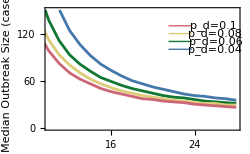

```mathematica
val=29;
y1=100;
dy=10;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1=21.5;
dx=2.25;
x2=26;
Show[ListLinePlot[{Table[FindMedianSize[sizedist4,i],{i,1,28}],Table[FindMedianSize[sizedist6,i],{i,1,28}],Table[FindMedianSize[sizedist8,i],{i,1,28}],Table[FindMedianSize[sizedist10,i],{i,1,28}]},Frame->True,PlotStyle->fourParamChartStyle,PlotRange->{{10,28},{0,150}},FrameLabel->{{"Median Outbreak Size (cases)",None},{"Days after detection","Estimates conditional on outbreak surviving"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x1+dx,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x1+dx,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x1+dx,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x1+dx,y1}}]}],Graphics[Text["p_d=0.1",{x2-0.15,y4}]],Graphics[Text["p_d=0.08",{x2,y3}]],Graphics[Text["p_d=0.06",{x2,y2}]],Graphics[Text["p_d=0.04",{x2,y1}]]]
```

```mathematica
Population size absolute at day 14
```

0

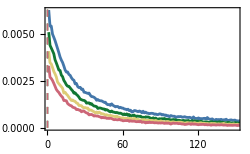

```mathematica
val=14;
s4=sizedist4[[val]];
s6=sizedist6[[val]];
s8=sizedist8[[val]];
s10=sizedist10[[val]];
s4[[;;,2]]=s4[[;;,2]]*(1-pend4[[val,2]]);
s6[[;;,2]]=s6[[;;,2]]*(1-pend6[[val,2]]);
s8[[;;,2]]=s8[[;;,2]]*(1-pend8[[val,2]]);
s10[[;;,2]]=s10[[;;,2]]*(1-pend10[[val,2]]);
s4[[1,2]]=pend4[[val,2]];
s6[[1,2]]=pend6[[val,2]];
s8[[1,2]]=pend8[[val,2]];
s10[[1,2]]=pend10[[val,2]];
(*Median outbreak sizes*)
cs4=s4;
For[i=2,i<=Length[s4],i++,
cs4[[i,2]]=cs4[[i,2]]+cs4[[i-1,2]];
];
cs6=s6;
For[i=2,i<=Length[s6],i++,
cs6[[i,2]]=cs6[[i,2]]+cs6[[i-1,2]];
];
cs8=s8;
For[i=2,i<=Length[s8],i++,
cs8[[i,2]]=cs8[[i,2]]+cs8[[i-1,2]];
];
cs10=s10;
For[i=2,i<=Length[s10],i++,
cs10[[i,2]]=cs10[[i,2]]+cs10[[i-1,2]];
];
cs4
Med[s_]:= Median[WeightedData[Map[First,s], Map[Last, s]]];
med4=Med[s4]
med6=Med[s6];
med8=Med[s8];
med10=Med[s10];
p1=Show[ListLinePlot[{s4[[2;;]],s6[[2;;]],s8[[2;;]],s10[[2;;]]},PlotRange->{{1,150},All},Frame->True,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Outbreak size (cases)","Day 14"}}, FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{13,y4},{15,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{13,y3},{15,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{13,y2},{15,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{13,y1},{15,y1}}]}],Graphics[Text["p_d=0.1",{17,y4}]],Graphics[Text["p_d=0.08",{17.2,y3}]],Graphics[Text["p_d=0.06",{17.2,y2}]],Graphics[Text["p_d=0.04",{17.2,y1}]],Graphics[{Dashed,fourParamChartStyle[[1]],Line[{{med4,0},{med4,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[2]],Line[{{med6,0},{med6,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[3]],Line[{{med8,0},{med8,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[4]],Line[{{med10,0},{med10,0.5}}]}]]
```

```mathematica
Time of spillover event
```

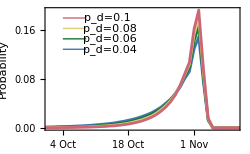

```mathematica
val=29;
y1=0.128;
dy=0.017;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1=-51;
dx=5;
x2=-41;
Show[ListLinePlot[{origdist4[[val]],origdist6[[val]],origdist8[[val]],origdist10[[val]]},PlotRange->{{-54,-14},All},Frame->True,Axes->False,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Date","Time of spillover event"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250,FrameTicks->{{Automatic,Automatic},{{{-23-28,"4 Oct"},{-23-21,"11 Oct"},{-23-14,"18 Oct"},{-23-7,"25 Oct"},{-23,"1 Nov"},{-23+7,"8 Nov"}},Automatic}}],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x1+dx,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x1+dx,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x1+dx,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x1+dx,y1}}]}],Graphics[Text["p_d=0.1",{x2-0.5,y4}]],Graphics[Text["p_d=0.08",{x2,y3}]],Graphics[Text["p_d=0.06",{x2,y2}]],Graphics[Text["p_d=0.04",{x2,y1}]]]
```

```mathematica
Maximum likelihood times relative to first observation
```

```mathematica
Sort[origdist4[[val]],#1[[2]]>#2[[2]]&][[1,1]]
Sort[origdist6[[val]],#1[[2]]>#2[[2]]&][[1,1]]
Sort[origdist8[[val]],#1[[2]]>#2[[2]]&][[1,1]]
Sort[origdist10[[val]],#1[[2]]>#2[[2]]&][[1,1]]
```

-22

-22

-22

«1 more identical outputs»

```mathematica
Mean times relative to first observation
```

```mathematica
Total[Table[origdist4[[val,i,1]]*origdist4[[val,i,2]],{i,1,Length[origdist4[[val]]]}]]
Total[Table[origdist6[[val,i,1]]*origdist6[[val,i,2]],{i,1,Length[origdist6[[val]]]}]]
Total[Table[origdist8[[val,i,1]]*origdist8[[val,i,2]],{i,1,Length[origdist8[[val]]]}]]
Total[Table[origdist10[[val,i,1]]*origdist10[[val,i,2]],{i,1,Length[origdist10[[val]]]}]]
```

-27.4154

-26.392

-25.7636

-25.3113

```mathematica
Final distribution of R0
```

{0.00576671,0.0126546,0.0211411,0.0319306,0.0455402,0.062748,0.0831953,0.106341,0.121842,0.12153,0.101688,0.0759091,0.0543472,0.0393158,0.0280422,0.020475,0.0154575,0.0115216,0.00879648,0.00672036,0.00524834,0.00417994,0.00316694,0.00247183,0.00200622,0.00153401,0.00131505,0.00102751,0.000812511,0.00067929,0.000563218,0.000507819,0.000361409,0.000267759,0.000208404,0.000221594,0.000150367,0.000121349,0.000110797,0.0000830977}

{{0.1,0.00576671},{0.2,0.0184213},{0.3,0.0395624},{0.4,0.071493},{0.5,0.117033},{0.6,0.179781},{0.7,0.262976},{0.8,0.369318},{0.9,0.49116},{1.,0.61269},{1.1,0.714377},{1.2,0.790287},{1.3,0.844634},{1.4,0.883949},{1.5,0.911992},{1.6,0.932467},{1.7,0.947924},{1.8,0.959446},{1.9,0.968242},{2.,0.974963},{2.1,0.980211},{2.2,0.984391},{2.3,0.987558},{2.4,0.99003},{2.5,0.992036},{2.6,0.99357},{2.7,0.994885},{2.8,0.995912},{2.9,0.996725},{3.,0.997404},{3.1,0.997967},{3.2,0.998475},{3.3,0.998837},{3.4,0.999104},{3.5,0.999313},{3.6,0.999534},{3.7,0.999685},{3.8,0.999806},{3.9,0.999917},{4.,1.}}

{{0.1,0.00576671},{0.2,0.0126546},{0.3,0.0211411},{0.4,0.0319306},{0.5,0.0455402},{0.6,0.062748},{0.7,0.0831953},{0.8,0.106341},{0.9,0.121842},{1.,0.12153},{1.1,0.101688},{1.2,0.0759091},{1.3,0.0543472},{1.4,0.0393158},{1.5,0.0280422},{1.6,0.020475},{1.7,0.0154575},{1.8,0.0115216},{1.9,0.00879648},{2.,0.00672036},{2.1,0.00524834},{2.2,0.00417994},{2.3,0.00316694},{2.4,0.00247183},{2.5,0.00200622},{2.6,0.00153401},{2.7,0.00131505},{2.8,0.00102751},{2.9,0.000812511},{3.,0.00067929},{3.1,0.000563218},{3.2,0.000507819},{3.3,0.000361409},{3.4,0.000267759},{3.5,0.000208404},{3.6,0.000221594},{3.7,0.000150367},{3.8,0.000121349},{3.9,0.000110797},{4.,0.0000830977}}

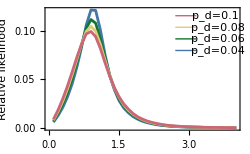

```mathematica
a4=accept4[[;;,-1,2]]/Total[accept4[[;;,-1,2]]]
ca4=a4;
For[i=2,i<=Length[ca4],i++,
ca4[[i]]=ca4[[i]]+ca4[[i-1]];
];
ca4=Partition[Riffle[Table[0.1*i,{i,1,40}],ca4],2]
a4=Partition[Riffle[Table[0.1*i,{i,1,40}],a4],2]

a6=accept6[[;;,-1,2]]/Total[accept6[[;;,-1,2]]];
ca6=a6;
For[i=2,i<=Length[ca6],i++,
ca6[[i]]=ca6[[i]]+ca6[[i-1]];
];
ca6=Partition[Riffle[Table[0.1*i,{i,1,40}],ca6],2];
a6=Partition[Riffle[Table[0.1*i,{i,1,40}],a6],2];

a8=accept8[[;;,-1,2]]/Total[accept8[[;;,-1,2]]];
ca8=a8;
For[i=2,i<=Length[ca8],i++,
ca8[[i]]=ca8[[i]]+ca8[[i-1]];
];
ca8=Partition[Riffle[Table[0.1*i,{i,1,40}],ca8],2];
a8=Partition[Riffle[Table[0.1*i,{i,1,40}],a8],2];

a10=accept10[[;;,-1,2]]/Total[accept10[[;;,-1,2]]];
ca10=a10;
For[i=2,i<=Length[ca10],i++,
ca10[[i]]=ca10[[i]]+ca10[[i-1]];
];
ca10=Partition[Riffle[Table[0.1*i,{i,1,40}],ca10],2];
a10=Partition[Riffle[Table[0.1*i,{i,1,40}],a10],2];

y1=0.08;
dy=0.012;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1=2.7;
dx=0.45;
x2=3.6;
Show[ListLinePlot[{a4,a6,a8,a10},Frame->True,Axes->False,PlotStyle->fourParamChartStyle,FrameLabel->{"R_0","Relative likelihood"},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x1+dx,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x1+dx,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x1+dx,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x1+dx,y1}}]}],Graphics[Text["p_d=0.1",{x2-0.05,y4}]],Graphics[Text["p_d=0.08",{x2,y3}]],Graphics[Text["p_d=0.06",{x2,y2}]],Graphics[Text["p_d=0.04",{x2,y1}]]]
```

```mathematica
Statistics of R0: Maximum likelihood
```

```mathematica
Sort[a4,#1[[2]]>#2[[2]]&][[1,1]]
Sort[a6,#1[[2]]>#2[[2]]&][[1,1]]
Sort[a8,#1[[2]]>#2[[2]]&][[1,1]]
Sort[a10,#1[[2]]>#2[[2]]&][[1,1]]
```

0.9

0.9

0.9

«1 more identical outputs»

```mathematica
Statistics of R0: 95 per cent confidence interval
```

```mathematica
ca4
```

{{0.1,0.00576671},{0.2,0.0184213},{0.3,0.0395624},{0.4,0.071493},{0.5,0.117033},{0.6,0.179781},{0.7,0.262976},{0.8,0.369318},{0.9,0.49116},{1.,0.61269},{1.1,0.714377},{1.2,0.790287},{1.3,0.844634},{1.4,0.883949},{1.5,0.911992},{1.6,0.932467},{1.7,0.947924},{1.8,0.959446},{1.9,0.968242},{2.,0.974963},{2.1,0.980211},{2.2,0.984391},{2.3,0.987558},{2.4,0.99003},{2.5,0.992036},{2.6,0.99357},{2.7,0.994885},{2.8,0.995912},{2.9,0.996725},{3.,0.997404},{3.1,0.997967},{3.2,0.998475},{3.3,0.998837},{3.4,0.999104},{3.5,0.999313},{3.6,0.999534},{3.7,0.999685},{3.8,0.999806},{3.9,0.999917},{4.,1.}}

```mathematica
{Select[ca4,#[[2]]<0.025&][[-1]],Select[ca4,#[[2]]>0.975&][[1]]}
{Select[ca6,#[[2]]<0.025&][[-1]],Select[ca6,#[[2]]>0.975&][[1]]}
{Select[ca8,#[[2]]<0.025&][[-1]],Select[ca8,#[[2]]>0.975&][[1]]}
{Select[ca10,#[[2]]<0.025&][[-1]],Select[ca10,#[[2]]>0.975&][[1]]}
```

{{0.2,0.0184213},{2.1,0.980211}}

{{0.2,0.0218272},{2.1,0.97704}}

{{0.2,0.0246347},{2.2,0.979584}}

{{0.1,0.00873164},{2.2,0.977666}}

```mathematica
Figure S2A
```

```mathematica
Changes in the inferred posterior distribution for R0 with time given Subscript[p, d]=0.04
```

```mathematica
col2=Table[RGBColor[{Cos[2.31x-0.69],Sin[2.926x],Sin[2.772x-0.144]}],{x,0,1,1/27}]
```

{RGBColor[{0.7712460149971067, 0., -0.14350285172336283}],RGBColor[{0.8228179496180482, 0.10815837547764777, -0.04132156505470021}],RGBColor[{0.8683707329153034, 0.2150477668137401, 0.06129488683700954}],RGBColor[{0.9075711331016849, 0.31941407841089964, 0.16326583067337896}],RGBColor[{0.9401323879100587, 0.42003281707805756, 0.263517391143535}],RGBColor[{0.9658163023422827, 0.5157234585779733, 0.3609938000882835}],RGBColor[{0.9844349911345216, 0.6053632983024981, 0.4546685149944325}],RGBColor[{0.9958522531923037, 0.6879006235704856, 0.5435550297083055}],RGBColor[{0.9999845679409262, 0.7623670530024181, 0.6267172635187739}],RGBColor[{0.9968017063026193, 0.8278888981982057, 0.7032794192004101}],RGBColor[{0.9863269518309961, 0.8836974144155966, 0.7724352061998417}],RGBColor[{0.9686369303851207, 0.9291378199815968, 0.8334563318341858}],RGBColor[{0.9438610495891844, 0.9636769786153176, 0.8857001710791458}],RGBColor[{0.9121805521782997, 0.9869096545282654, 0.9286165341747794}],RGBColor[{0.8738271901554634, 0.9985632669131823, 0.961753460778003}],RGBColor[{0.8290815294586145, 0.9985010880386929, 0.9847619796425122}],RGBColor[{0.7782708975396367, 0.986723847427641, 0.9973997837010308}],RGBColor[{0.7217669888693595, 0.9633697232978549, 0.9995337818469013}],RGBColor[{0.6599831458849821, 0.9287127213657643, 0.9911415005417208}],RGBColor[{0.593371335270574, 0.8831594600337951, 0.9723113204884275}],RGBColor[{0.522418841690038, 0.827244399679806, 0.9432415458773894}],RGBColor[{0.44764470315883353, 0.7616235720216362, 0.90423831600744}],RGBColor[{0.36959591413074766, 0.6870668831279216, 0.8557123812749748}],RGBColor[{0.28884342407523306, 0.6044490803812398, 0.7981747774837799}],RGBColor[{0.20597796081687653, 0.5147394893750344, 0.7322314440302518}],RGBColor[{0.12160570919047721, 0.4189906411576828, 0.6585768426409192}],RGBColor[{0.03634387662362632, 0.3183259232562573, 0.5779866438645533}],RGBColor[{-0.049183821914170554, 0.2139263993661666, 0.4913095583387953}]}

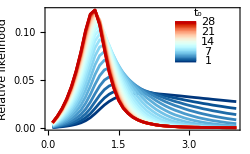

```mathematica
postt=Table[accept4[[;;,i,2]]/Total[accept4[[;;,i,2]]],{i,1,28}];
For[i=1,i<=Length[postt],i++,
postt[[i]]=Partition[Riffle[Table[i,{i,0.1,4.0,0.1}],postt[[i]]],2];
];

Show[ListLinePlot[postt,PlotRange->All,PlotStyle->Reverse[col2],Frame->True,FrameLabel->{"R_0","Relative likelihood"},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Table[Graphics[{Reverse[col2][[i]],Thickness[0.008],Line[{{2.7,0.07+0.0015*(i-1)},{3.15,0.07+0.0015*(i-1)}}]}],{i,1,28}],Graphics[Text["1",{3.4,0.07}]],Graphics[Text["7",{3.4,0.07+0.0015*6}]],Graphics[Text["14",{3.4,0.07+0.0015*13}]],Graphics[Text["21",{3.4,0.07+0.0015*20}]],Graphics[Text["28",{3.4,0.07+0.0015*27}]],Graphics[Text["t_o",{3.2,0.12}]]]
```

```mathematica
Figure S2B
```

```mathematica
Changes in the inferred time of first infection with time given Subscript[p, d]=0.04
```

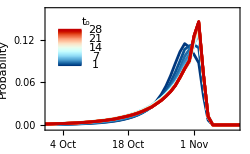

```mathematica
val=29;
y1=0.128;
dy=0.017;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1=-51;
dx=5;
x2=-41;
yy=0.085;
dyy=0.0018;
Show[Table[ListLinePlot[{origdist4[[val]]},PlotRange->{{-54,-14},{-0.004,0.162}},Frame->True,Axes->False,PlotStyle->Reverse[col2][[val]],FrameLabel->{{"Probability",None},{"Date","Time of spillover event"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250,FrameTicks->{{Automatic,Automatic},{{{-23-28,"4 Oct"},{-23-21,"11 Oct"},{-23-14,"18 Oct"},{-23-7,"25 Oct"},{-23,"1 Nov"},{-23+7,"8 Nov"}},Automatic}}],{val,1,28}],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x1+dx,y4}}]}],Table[Graphics[{Reverse[col2][[i]],Thickness[0.008],Line[{{-52,yy+dyy*(i-1)},{-47,yy+dyy*(i-1)}}]}],{i,1,28}],Graphics[Text["1",{-44,yy}]],Graphics[Text["7",{-44,yy+dyy*6}]],Graphics[Text["14",{-44,yy+dyy*13}]],Graphics[Text["21",{-44,yy+dyy*20}]],Graphics[Text["28",{-44,yy+dyy*27}]],Graphics[Text["t_o",{-46,0.145}]]]
```